◼ "\◼ "2024-07-01T16:13v1 .10M. J. Steil[msteil@theorie.ikp.physik.tu-darmstadt.de](mailto:msteil@theorie.ikp.physik.tu-darmstadt.de)TU Darmstadt

# Gross-Neveu model

Martin Jakob Steil^1

^1Technische Universität Darmstadt

[M. J. Steil, - 2024 - PhD thesis]

Initialization

Clear["Global`*"]

```mathematica
SetDirectory[NotebookDirectory[]];
$DistributedContexts={};
```

```mathematica
(* Disable Notebookhistory, [https://mathematica.stackexchange.com/questions/11258/are-there-suitable-versioning-systems-for-mathematica-notebooks]*)
SetOptions[EvaluationNotebook[],PrivateNotebookOptions->{"FileOutlineCache"->False},System`TrackCellChangeTimes->False]

(* Display the Timing of an Evaluation in a Notebook Window [https://reference.wolfram.com/language/howto/DisplayTheTimingOfAnEvaluationInANotebookWindow.html] *)
SetOptions[EvaluationNotebook[],EvaluationCompletionAction->{"ShowTiming"}]
```

```mathematica
(* SaveToCell | v2.0 | Save assigned value of symbol(s) to cell(s) | Modified Version of [http://szhorvat.net/pelican/save-data-in-notebooks.html] *)
ClearAll[SaveToCell];
SaveToCell[names_/;VectorQ[names,StringQ],suffix:Except[_?OptionQ]:"",comment:Except[_?OptionQ]:"",opt:OptionsPattern[]]:=Module[{
	data=Symbol[#]&/@names,
	label=Row[Flatten@{If[comment=!="",{Style[comment,Plain],", "},Nothing],DateString["ISODateTime"]}]
	},
	CellPrint@Cell[
		BoxData@MapThread[RowBox[{#2<>suffix,"=",ToBoxes[Iconize[#1,label,Method->Compress]],";"}]&,{data,names}],
		"Input",
		GeneratedCell->False,(*prevent deletion by Cell>Delete All Output:*)
		CellLabel->"(saved)",
		CellLabelAutoDelete->False,
		opt
	]
]

SetAttributes[SaveToCell,HoldFirst]
SaveToCell[var_,name:Except[_?OptionQ]:"",comment:Except[_?OptionQ]:"",opt:OptionsPattern[]]:=With[{
	data=Evaluate[var],
	label=Row[Flatten@{If[comment=!="",{Style[comment,Plain],", "},Nothing],DateString["ISODateTime"]}]
	},
	CellPrint@Cell[
		BoxData@RowBox[{If[name=!="",name,MakeBoxes[var]],"=",ToBoxes[Iconize[data,label,Method->Compress]],";"}],
		"Input",
		GeneratedCell->False,(*prevent deletion by Cell>Delete All Output:*)
		CellLabel->"(saved)",
		CellLabelAutoDelete->False,
		opt
	]
]
SaveToCell::usage="SaveToCell[var_,name:Except[_?OptionQ]:\"\",comment:Except[_?OptionQ]:\"\",opt:OptionsPattern[]]: saves the assignment of var/or the data in\
 var (under name if name=!=\"\") in a compressed iconized form with a label including comment and a time stamp.\n\
SaveToCell[names_/;VectorQ[names,StringQ],suffix_:Except[_?OptionQ]:\"\",comment:Except[_?OptionQ]:\"\",opt:OptionsPattern[]]: saves the assignments behind the elements of names in\
 in a compressed iconized form with suffix appended to the symbol names and a label including comment and a time stamp.";
```

```mathematica
(* AutoCollapse | v2.0 | Close CellGroup | [https://mathematica.stackexchange.com/a/683] *)
AutoCollapse[]:=Module[{},
	If[$FrontEnd=!=$Failed,
		SelectionMove[EvaluationNotebook[],All,GeneratedCell];
		FrontEndTokenExecute["SelectionCloseUnselectedCells"]
	];
]
AutoCollapse::usage="Collapse input cells by grouping them with the generated output cells.";
```

```mathematica
(* CellPrintDisplayFormulaNumbered | v2.3 | CellPrint a DisplayFormulaNumbered *)
ClearAll[CellPrintDisplayFormulaNumbered,CellPrintDisplayFormulaNumberedNAC];
CellPrintDisplayFormulaNumbered[exp_,tag_:None,comment_:"",generatedCellQ_:False,groupQ_:True,autoCollapseQ_:True]:=Module[{frameLabels,box},
	frameLabels=CellFrameLabels->{
		{None,Cell[TextData[{If[tag===None,"",ToString[tag]<>" "]<>"(",CounterBox["Chapter"],".",CounterBox["DisplayFormulaNumbered"],")"}],"DisplayFormulaEquationNumber"]},
		{None,None}
	};
	box=BoxData[RowBox[{ToBoxes[exp],RowBox[{comment}]}]];
	CellPrint[Cell[box,"DisplayFormulaNumberedPrinted",frameLabels,
		GeneratedCell->generatedCellQ,CellAutoOverwrite->True,ShowStringCharacters->False,CellGroupingRules->If[groupQ,"OutputGrouping",Inherited]]
	];
	If[autoCollapseQ,AutoCollapse[]];
]
CellPrintDisplayFormulaNumbered::usage="CellPrintDisplayFormulaNumbered[exp_,tag_:None,comment_:\"\",generatedCellQ_:False,groupQ_:True,autoCollapseQ_:True]:\
CellPrint exp to a DisplayFormulaNumberedPrinted output cell.";
CellPrintDisplayFormulaNumberedNAC[exp_,tag_:None,comment_:"",generatedCellQ_:False,groupQ_:True,autoCollapseQ_:False]:=CellPrintDisplayFormulaNumbered[exp,tag,comment,generatedCellQ,groupQ,autoCollapseQ]
CellPrintDisplayFormulaNumberedNAC::usage="Same as CellPrintDisplayFormulaNumbered[] but autoCollapseQ defaults to false.";
```

```mathematica
(* GetCodePackage | v1.1 | Get CodePackage Cells from a notebook *)
GetCodePackage[file_String,tags_:{},groupQ_:True]:=Module[{nb,cells},
	nb=NotebookOpen[AbsoluteFileName[file],Visible->False];
	NotebookFind[nb,"CodePackage",All,CellStyle];
	cells=NotebookRead[nb];
	cells=Flatten[{cells}];
	If[tags=!={},
		cells=Select[cells,ContainsAny[{#/.Cell[x___,CellTags->t_,y___]:>t}//Flatten,tags]&];
	];	
	NotebookClose[nb];
	
	CellPrint[Cell[BoxData[ RowBox[{
		"(** "<>file<>" from "<>DateString["ISODateTime"]<>" imported using **)\n(*GetCodePackage[\""<>file<>"\","<>ToString@tags<>","<>ToString@groupQ<>"]*)"
	}]], "CodePackage"]];
	CellPrint[Reverse[cells]/.Cell[x__]:>Cell[x,GeneratedCell->False,CellGroupingRules->If[groupQ,"OutputGrouping",Inherited]]];
	
	If[$FrontEnd=!=$Failed,
		SelectionMove[EvaluationNotebook[],All,GeneratedCell];
		FrontEndTokenExecute["SelectionCloseUnselectedCells"]
	];
	NotebookDelete[EvaluationCell[]]
]
GetCodePackage::usage="GetCodePackage[file_String,tags_:{},groupQ_:True]: Get all CodePackage Cells from file and CellPrint them.";
```

```mathematica
(* DefinedQ | v1.4 | Check wether a symbol is defined, i.e. has a Value, Down-, Up=, and/or OwnValues. *)
ClearAll[DefinedQ];
DefinedQ[symbol_Symbol]:=ValueQ[symbol]||DownValues[symbol]=!={}||UpValues[symbol]=!={}||OwnValues[symbol]=!={}
DefinedQ[symbol_String]:=Quiet[Check[
	ValueQ[Evaluate[Symbol[symbol]]]||DownValues[Evaluate[Symbol[symbol]]]=!={}||UpValues[Evaluate[Symbol[symbol]]]=!={}||OwnValues[Evaluate[Symbol[symbol]]] =!= {},
False], Symbol::sym]
DefinedQ[symbols_List]:=And@@Map[DefinedQ,symbols]
DefinedQ::usage="DefinedQ[symbol_]: Check wether a symbol is defined, i.e. has a Value, Down-, Up=, and/or OwnValues.";
```

```mathematica
(* AddOptions | v1.0 |  Add Option values to a symbol *)
AddOptions[x_,option_Rule]:=If[MemberQ[Options[x]/.Rule[a_,b_]:>a,option[[1]]],SetOptions[x,option],Options[x]=Join[Options[x],{option}]];
AddOptions[x_,option_List]:=AddOptions[x,#]&/@option;
AddOptions[x_,option__]:=AddOptions[x,{option}]
LookupOption::usage="AddOptions[x_,option_Rule]: Adds option to the list of Options[x].";
```

{
	"NCM","CM","contraction","FS`type",(*selected basics*)
	"FRG`wetterichEq`FS0","FRG`wetterichEq`FS1","FRG`wetterichEq`FS2","FRG`wetterichEq`FS3","FRG`wetterichEq`FS4", (* super field flow equations *)
	"FRG`diagramGraph","FRG`diagramCircularGraphics","FRG`diagramAxodraw2"(* Plotting utlities *)
};
If[!DefinedQ[Evaluate@%],
	MessageDialog[
		Row[{"WARNING: This notebook needs a version of the field space notebook (e.g. fs_20231122.nb) already executed — sorry that the code is not packaged jet."}],
		WindowTitle -> "Error — "EvaluatorAbort""
	];
	FrontEndExecute[FrontEndToken["EvaluatorAbort"]]
]

## Gross-Neveu model Feynman rules and relevant diagrams

### Diagram styles

```mathematica
GN2`q=FS`field["ψ",List[FS`type`fermionic]];
GN2`q[α_,cQ_:True]:=comp[GN2`q,{idx[GN2`qidxs,α,cQ]}]
GN2`qb=FS`field["ψ",List[FS`type`fermionic,FS`type`adjoint]];
GN2`qb[α_,cQ_:True]:=comp[GN2`qb,{idx[GN2`qbidxs,α,cQ]}]

GN2`σ=FS`field["σ",List[FS`type`bosonic]];
GN2`σ[α_,cQ_:True]:=comp[GN2`σ,{idx[GN2`σidxs,α,cQ]}]

GN2`fieldsSummationInformation={{GN2`q,GN2`qidxs},{GN2`qb,GN2`qbidxs},{GN2`σ,GN2`σidxs}};
```

```mathematica
numbers=ToString[#]&/@Range[3];
romans=RomanNumeral[#]&/@Range[3];
(* Index for fermions *)
Options[GN2`qidxs]={
	"idx`format"->idx`format`alphabetic[#&/@numbers,Style[#,{Black,Underlined}]&/@romans,"f"],
	"idx`formatTeX"->idx`formatTeX`alphabetic[
		StringRiffle[{ToString@TeXForm[#]},{"{","","}"}]&/@numbers,
		StringRiffle[{ToString@TeXForm[#]},{"\\underline{","","}"}]&/@romans,
	"f"]
};
Options[GN2`qbidxs]={
	"idx`format"->idx`format`alphabetic[#&/@numbers,Style[#,{Black,Underlined}]&/@romans,"f"],
	"idx`formatTeX"->idx`formatTeX`alphabetic[
		StringRiffle[{ToString@TeXForm[#]},{"{","","}"}]&/@numbers,
		StringRiffle[{ToString@TeXForm[#]},{"\\underline{","","}"}]&/@romans,
	"f"]
};
(* Index for sigma *)
Options[GN2`σidxs]={
	"idx`format"->idx`format`alphabetic[#&/@numbers,Style[#,{Black,Underlined}]&/@romans,"i"],
	"idx`formatTeX"->idx`formatTeX`alphabetic[
		StringRiffle[{ToString@TeXForm[#]},{"{","","}"}]&/@numbers,
		StringRiffle[{ToString@TeXForm[#]},{"\\underline{","","}"}]&/@romans,
	"f"]
};
```

```mathematica
Options[FRG`diagramGraph]={	
	"PropagatorStyles"->{
		comp[FS`propagator[],{comp[GN2`q,μf__],μ__}]:>{Thick,GUCD`gruen},
		comp[FS`propagator[],{comp[GN2`qb,μf__],μ__}]:>{Thick,GUCD`gruen},
		comp[FS`propagator[],{comp[GN2`σ,μf__],μ__}]:>{Thick,GUCD`goetheBlau}
	},
	"NodeStyles"->{
		comp[FS`regulator[r_],{comp[GN2`σ,μf__],μ__}]:>{EdgeForm[{Thick,GUCD`goetheBlau}],White},
		comp[FS`regulator[r_],{comp[f_/;FS`type`fermionicQ[f],μf__],μ__}]:>{EdgeForm[{Thick,GUCD`gruen}],White},
		comp[FS`vertex[],μ__]:>{EdgeForm[{Thick,Black}],White}
	},
	"ExternalLegStyles"->{
		comp[q_,μf__]:>{Thick,GUCD`gruen}/;MemberQ[{GN2`qb,GN2`q},q],
		comp[GN2`σ,μf__]|GN2`σidxs:>{Thick,GUCD`goetheBlau}
	}
};
GN2`FRG`diagramGraphDefault=Options[FRG`diagramGraph];
```

```mathematica
FRG`diagramAxodraw2//Options={
	"widthFactor" -> 12,
	"externalLeg`labelFunctions"->{
		comp[GN2`qb,{idx[GN2`qbidxs,μ_,cQ_]}]:>Function[{s,x},
			"\\Text"<>Axodraw2`point[x,1]<>"{\\raisebox{-8pt}{$\\bar{\\psi}_{"<>If[!cQ,"\\underline",""]<>"{\\scriptscriptstyle{"<>ToString[TeXForm[romans[[μ+1]]]]<>"}}}$}}"
		],
		comp[GN2`q,{idx[GN2`qidxs,μ_,cQ_]}]:>Function[{s,x},
			"\\Text"<>Axodraw2`point[x,1]<>"{\\raisebox{+2pt}{$\\psi^{"<>If[!cQ,"\\underline",""]<>"{\\scriptscriptstyle{"<>ToString[TeXForm[romans[[μ+1]]]]<>"}}}$}}"
		],
		comp[GN2`σ,{idx[GN2`σidxs,μ_,cQ_]}]|GN2`σ:>Function[{s,x},
			"\\Text"<>Axodraw2`point[x,1]<>"{\\raisebox{0pt}{$\\sigma_{"<>If[!cQ,"\\mkern-2mu\\underline",""]<>"{\\scriptscriptstyle{"<>ToString[TeXForm[romans[[μ+1]]]]<>"}}}$}}"
		]			
	},
	"arcedPropagator`shapes"->{
		comp[GN2`σ,{idx[GN2`σidxs,μ_,cQ_]}]|GN2`σ :> Function[{s,x,y,lineStyles},
			"\\ZigZag["<>lineStyles<>"]"<>Axodraw2`point[x,1]<>Axodraw2`point[y,1]<>"{1}{"<>ToString[Ceiling[Norm[y-x]*1/4]]<>"}"
		]
	},
	
	"externalLeg`shapes"->{
		comp[GN2`σ,{idx[GN2`σidxs,μ_,cQ_]}]|GN2`σ :> Function[{s,x,y,lineStyles},
			"\\ZigZag["<>lineStyles<>"]"<>Axodraw2`point[x,1]<>Axodraw2`point[y,1]<>"{1}{"<>ToString[Ceiling[Norm[y-x]*1/4]]<>"}"
		]
	},
	"arcedPropagator`shapes"->{
		comp[FS`propagator[],{comp[GN2`σ,μf__],μ__}]:>Function[{s,r,θ1,θ2,lineStyles},
			"\\ZigZagArc["<>lineStyles<>"](0,0)"<>StringRiffle[ToString/@{r,θ1,θ2},{"(",",",")"}]<>"{1}{"<>ToString[Ceiling[Axodraw2`angleDistance[θ1,θ2]*10/180]]<>"}"
		]
	}
};
GN2`FRG`diagramAxodraw2Default=Options[FRG`diagramAxodraw2];
```

### ZeroPtFlow

```mathematica
List@@FRG`wetterichEq`FS0;
1/2*%;
contraction`sum[%,FS`idx,GN2`fieldsSummationInformation]//FRG`canonicalOrder//contraction`simplify;
List@@%[[2]];
GN2`Uflow=%//(LabelValues[#,"GN2`UFlow","LabelPostion"->{{Bottom,Center}}]&)

%//FRG`diagramGraph;
%//FRG`diagramCircularGraphics[#,PlotRange->3*{{-1,1},{-1,1}},ImageSize->75,"PostProcessFunction"->Function[x,GraphicsChop[x,Symmetric->False,ImagePadding->{0.04,0.04}]]]&

FRG`diagramAxodraw2`draw[%]
ParallelMap[FRG`diagramAxodraw2`compile[#,"../gn/diagrams","gn/diagrams"]&,%,Method->"FinestGrained"]
```

{  -  G_t_(;ψ_1ψ̄_1)∂_t R_t^(;ψ_1ψ̄_1)GN2`UFlow[[1]],  1/2  G_t_(;σ_1σ_1)∂_t R_t^(;σ_1σ_1)GN2`UFlow[[2]]}

{- -Graphics-,1/2 -Graphics-}

{FRG`diagramAxodraw2[…],FRG`diagramAxodraw2[…]}

{FRG`diagramAxodraw2[…],FRG`diagramAxodraw2[…]}

### TwoPtFlow

```mathematica
AddOptions[FRG`diagramCircularGraphics,"externalLegs`radiusFactor2" -> 1.4];
List@@FRG`wetterichEq`FS2/.{
	FS`idx[0,False]->comp[GN2`σ,idx[GN2`σidxs,1,False]],
	FS`idx[1,False]->comp[GN2`σ,idx[GN2`σidxs,0,False]]
};
GN2`TwoPtFlow`FS=Equal@@(Expand[1/2*List@@%]);
contraction`sum[%[[2,2]],FS`idx,GN2`fieldsSummationInformation]//FRG`canonicalOrder//contraction`simplify;
GN2`TwoPtFlow=(List@@%)//(LabelValues[#,"GN2`TwoPtFlow","LabelPostion"->{{Bottom,Center}}]&);

%//FRG`diagramGraph;
%//FRG`diagramCircularGraphics[#,PlotRange->3*{{-1,1},{-1,1}},ImageSize->75,"PostProcessFunction"->Function[x,GraphicsChop[x,Symmetric->False]]]&

FRG`diagramAxodraw2`draw[%]
ParallelMap[FRG`diagramAxodraw2`compile[#,"../gn/diagrams","gn/diagrams"]&,%,Method->"FinestGrained"]
```

{-1/2 -Graphics-,-1/2 -Graphics-,1/2 -Graphics-}

{FRG`diagramAxodraw2[…],FRG`diagramAxodraw2[…],FRG`diagramAxodraw2[…]}

{FRG`diagramAxodraw2[…],FRG`diagramAxodraw2[…],FRG`diagramAxodraw2[…]}

```mathematica
GN2`TwoPtFlow[[1]]
```

-1/2  G_t_(;ψ_1ψ̄_1)Γ̄_t^(,ψ̄_1σ_Iψ_2)G_t_(;ψ_2ψ̄_2)Γ̄_t^(,ψ̄_2σ_IIψ_3)G_t_(;ψ_3ψ̄_3)∂_t R_t^(;ψ_1ψ̄_3)GN2`TwoPtFlow[[1]]

### Regulator insertions

```mathematica
FRG`diagramAxodraw2//Options={
	"widthFactor" -> 12,
	"externalLeg`labelFunctions"->{
		comp[GN2`qb,{idx[GN2`qbidxs,μ_,cQ_]}]:>Function[{s,x},
			"\\Text"<>Axodraw2`point[x,1]<>"{\\raisebox{-8pt}{$\\bar{\\psi}_{"<>If[!cQ,"\\underline",""]<>"{\\scriptscriptstyle{"<>ToString[TeXForm[romans[[μ+1]]]]<>"}}}$}}"
		],
		comp[GN2`q,{idx[GN2`qidxs,μ_,cQ_]}]:>Function[{s,x},
			"\\Text"<>Axodraw2`point[x,1]<>"{\\raisebox{+2pt}{$\\psi^{"<>If[!cQ,"\\underline",""]<>"{\\scriptscriptstyle{"<>ToString[TeXForm[romans[[μ+1]]]]<>"}}}$}}"
		],
		comp[GN2`σ,{idx[GN2`σidxs,μ_,cQ_]}]|GN2`σ:>Function[{s,x},
			"\\Text"<>Axodraw2`point[x,1]<>"{\\raisebox{-2pt}{$\\sigma_{"<>If[!cQ,"\\mkern-2mu\\underline",""]<>"{\\scriptscriptstyle{"<>ToString[TeXForm[romans[[μ+1]]]]<>"}}}$}}"
		]			
	},
	"arcedPropagator`shapes"->{
		comp[GN2`σ,{idx[GN2`σidxs,μ_,cQ_]}]|GN2`σ :> Function[{s,x,y,lineStyles},
			"\\ZigZag["<>lineStyles<>"]"<>Axodraw2`point[x,1]<>Axodraw2`point[y,1]<>"{1}{"<>ToString[Ceiling[Norm[y-x]*1/4]]<>"}"
		]
	},
	
	"externalLeg`shapes"->{
		comp[GN2`σ,{idx[GN2`σidxs,μ_,cQ_]}]|GN2`σ :> Function[{s,x,y,lineStyles},
			"\\ZigZag["<>lineStyles<>"]"<>Axodraw2`point[x,1]<>Axodraw2`point[y,1]<>"{1}{"<>ToString[Ceiling[Norm[y-x]*1/4]]<>"}"
		]
	},
	"arcedPropagator`shapes"->{
		comp[FS`propagator[],{comp[GN2`σ,μf__],μ__}]:>Function[{s,r,θ1,θ2,lineStyles},
			"\\ZigZagArc["<>lineStyles<>"](0,0)"<>StringRiffle[ToString/@{r,θ1,θ2},{"(",",",")"}]<>"{1}{"<>ToString[Ceiling[Axodraw2`angleDistance[θ1,θ2]*10/180]]<>"}"
		]
	}
};
GN2`FRG`diagramAxodraw2Default=Options[FRG`diagramAxodraw2];
```

```mathematica
Options[FRG`diagramCircularGraphics]={
	"externalLegs`radiusFactor0"->1.0, (*relative in this case to the regulator insertion radius -- default is 0.325*)
	"externalLegs`radiusFactor1" -> 3.0,
	"externalLegs`radiusFactor2" -> 4.9
};

comp[FS`regulator[],{GN2`q[0,False],GN2`qb[1,False]}]
FRG`diagramCircularGraphics[%,ImageSize->125,PlotRange->{{-2.75,2.75},{-2.75,2.75}},"PostProcessFunction"->(GraphicsChop[#,ImagePadding->{0.03,0.05}]&),Label->"GN2-Rttb"]
%[[2]];
FRG`diagramAxodraw2`draw[%];
FRG`diagramAxodraw2`compile[%,"../appendix/diagrams","appendix/diagrams","-3"]

Options[FRG`diagramCircularGraphics]={
	"externalLegs`radiusFactor0"->1.0, (*relative in this case to the regulator insertion radius -- default is 0.325*)
	"externalLegs`radiusFactor1" -> 3.2,
	"externalLegs`radiusFactor2" -> 4.9
};
comp[FS`regulator[],{GN2`σ[0,False],GN2`σ[1,False]}]
FRG`diagramCircularGraphics[%,ImageSize->125,PlotRange->{{-2.75,2.75},{-2.75,2.75}},"PostProcessFunction"->(GraphicsChop[#]&),Label->"GN2-Rss"]
%[[2]];
FRG`diagramAxodraw2`draw[%];
FRG`diagramAxodraw2`compile[%,"../appendix/diagrams","appendix/diagrams","-3"]
```

∂_t R_t^(;ψ_Iψ̄_II)

-Graphics-

FRG`diagramAxodraw2[…]

∂_t R_t^(;σ_Iσ_II)

-Graphics-

FRG`diagramAxodraw2[…]

### Two point functions

```mathematica
Options[FRG`diagramCircularGraphics]={
	"externalLegs`radiusFactor0"->0.25,
	"externalLegs`radiusFactor1"->0.95,
	"externalLegs`radiusFactor2"->1.625
};

comp[FS`vertex[],{GN2`qb[0,False],GN2`q[1,False]}]
test=FRG`diagramCircularGraphics[%,ImageSize->125,PlotRange->3*{{-1,1},{-1,1}},"PostProcessFunction"->(GraphicsChop[#,ImagePadding->{0.03,0.05}]&),Label->"GN2-Gamma2tbt"]
%[[2]];
FRG`diagramAxodraw2`draw[%];
FRG`diagramAxodraw2`compile[%,"../appendix/diagrams","appendix/diagrams","-3"]

Options[FRG`diagramCircularGraphics]={
	"externalLegs`radiusFactor0"->0.25,
	"externalLegs`radiusFactor1"->1.05,
	"externalLegs`radiusFactor2"->1.625
};
comp[FS`vertex[],{GN2`σ[0,False],GN2`σ[1,False]}]
test=FRG`diagramCircularGraphics[%,ImageSize->125,PlotRange->3*{{-1,1},{-1,1}},"PostProcessFunction"->(GraphicsChop[#]&),Label->"GN2-Gamma2ss"]
%[[2]];
FRG`diagramAxodraw2`draw[%];
FRG`diagramAxodraw2`compile[%,"../appendix/diagrams","appendix/diagrams","-3"]
```

Γ̄_t^(,ψ̄_Iψ_II)

-Graphics-

FRG`diagramAxodraw2[…]

Γ̄_t^(,σ_Iσ_II)

-Graphics-

FRG`diagramAxodraw2[…]

### Propagators

```mathematica
Options[FRG`diagramCircularGraphics]={
	"externalLegs`radiusFactor0"->0,
	"externalLegs`radiusFactor1"->0,
	"externalLegs`radiusFactor2"->0.95,
	"radiusFunction"->(0.8&)
};

comp[FS`propagator[],{GN2`q[0,False],GN2`qb[1,False]}]
test=FRG`diagramCircularGraphics[%,ImageSize->125,PlotRange->3*{{-1,1},{-1,1}},"PostProcessFunction"->(GraphicsChop[#,ImagePadding->{0.03,0.05}]&),Label->"GN2-Gttb"]
%[[2]];
FRG`diagramAxodraw2`draw[%];
FRG`diagramAxodraw2`compile[%,"../appendix/diagrams","appendix/diagrams","-3"]
```

G_t_(;ψ_Iψ̄_II)

-Graphics-

FRG`diagramAxodraw2[…]

```mathematica
Options[FRG`diagramCircularGraphics]={
	"externalLegs`radiusFactor0"->0,
	"externalLegs`radiusFactor1"->0,
	"externalLegs`radiusFactor2"->0.6,
	"radiusFunction"->(0.9&)
};

comp[FS`propagator[],{GN2`σ[0,False],GN2`σ[1,False]}]
test=FRG`diagramCircularGraphics[%,ImageSize->125,"PostProcessFunction"->(GraphicsChop[#]&),PlotRange->{{-2.75,2.75},{-2.75,2.75}},Label->"GN2-Gss"]
%[[2]];
FRG`diagramAxodraw2`draw[%];
FRG`diagramAxodraw2`compile[%,"../appendix/diagrams","appendix/diagrams","-3"]
```

G_t_(;σ_Iσ_II)

-Graphics-

FRG`diagramAxodraw2[…]

### Vertices

```mathematica
Options[FRG`diagramCircularGraphics]={"externalLegs`radiusFactor1"->1.0,"externalLegs`radiusFactor2"->1.6};
comp[FS`vertex[],{GN2`qb[0,False],GN2`σ[1,False],GN2`q[2,False]}]
FRG`diagramCircularGraphics[%,ImageSize->125,PlotRange->4*{{-1,1},{-1,1}},"PostProcessFunction"->(GraphicsChop[#,Symmetric->"y",ImagePadding->{0.04,0.04}]&),Label->"GN2-Vtbst"]
FRG`diagramAxodraw2`compile[FRG`diagramAxodraw2`draw@%,"../appendix/diagrams","appendix/diagrams","-3"]
```

Γ̄_t^(,ψ̄_Iσ_IIψ_III)

-Graphics-

FRG`diagramAxodraw2[…]

## Gross-Neveu model (s=1,D=1+1,d=2) (g)GL expansion around Δ=0 (,∂_xΔ[x]=0)

## Import of nb`, nf`, Actor` and GL` CodePackages

(** tqft_20231122.nb from 2023-12-09T01:11:13 imported using **)
(*GetCodePackage["tqft_20231122.nb",{},True]*)

ClearAll["nb","nb`*"]
nb`ωn[n_,β_:β]:=(2π)/β(n)

nb`expRule=nb[x_]:>1/(Exp[x]-1);
nb`expRuleInv=Exp[x_]:>(1+nb[x])/nb[x];
nb`trigRule=nb[x_]:>1/2(Coth[x/2]-1);
nb`trigRuleInv=Coth[x_]:>1+2nb[2x];

nb[x]/.nb`expRule/.nb`expRuleInv//Simplify;
nb[x]/.nb`trigRule/.nb`trigRuleInv//Simplify;

nblist={{nb[x],(nb[x]/.nb`trigRule),nb[x]}};
nblist=nblist~Join~{With[{d=D[nblist[[-1]],x]},{d[[1]],d[[2]],Simplify@TrigToExp[d[[2]]]/.nb`expRuleInv//Simplify}]};
nblist=nblist~Join~{With[{d=D[nblist[[-1]],x]},{d[[1]],d[[2]],FullSimplify[d[[3]]/.MapThread[#1→#2&,{nblist[[;;,1]],nblist[[;;,3]]}]]}]};
nblist=nblist~Join~{With[{d=D[nblist[[-1]],x]},{d[[1]],d[[2]],FullSimplify[d[[3]]/.MapThread[#1→#2&,{nblist[[;;,1]],nblist[[;;,3]]}]]}]};
nb`derivativeRules=(Inactive[RuleDelayed][#[[1]]/.x->Pattern[x,Blank[]],#[[2]]])&/@nblist[[2;;]][[All,{1,3}]]//Activate;
nb`derivativeTrigRules={nb`trigRule}~Join~Activate[(Inactive[RuleDelayed][#[[1]]/.x->Pattern[x,Blank[]],#[[2]]])&/@nblist[[2;;]][[All,{1,2}]]];

nbpowers=First@Solve[Expand[Equal@@#&/@nblist[[2;;,{1,3}]]]/.Array[nb[x]^(#+1)→nb_(#+1)&,Length[nblist]-1],Array[nb_(#+1)&,Length[nblist]-1]]/.Array[nb_(#+1)->nb[x]^(#+1)&,Length[nblist]-1];
nb`powersRules=(Inactive[RuleDelayed][#[[1]]/.x->Pattern[x,Blank[]],#[[2]]])&/@%//Activate;

ClearAll[nblist,nbpowers]

ClearAll["nf","nf`*"]
nf`νn[n_,β_:β]:=(2π)/β(n+1/2)

nf`expRule=nf[x_]:>1/(Exp[x]+1);
nf`expRuleInv=Exp[x_]:>(1-nf[x])/nf[x];
nf`trigRule=nf[x_]:>1/2(1-Tanh[x/2]);
nf`trigRuleInv=Tanh[x_]:>1-2nf[2x];

nf[x]/.nf`expRule/.nf`expRuleInv//Simplify;
nf[x]/.nf`trigRule/.nf`trigRuleInv//Simplify;

nflist={{nf[x],(nf[x]/.nf`trigRule),nf[x]}};
nflist=nflist~Join~{With[{d=D[nflist[[-1]],x]},{d[[1]],d[[2]],Simplify@TrigToExp[d[[2]]]/.nf`expRuleInv//Simplify}]};
nflist=nflist~Join~{With[{d=D[nflist[[-1]],x]},{d[[1]],d[[2]],FullSimplify[d[[3]]/.MapThread[#1→#2&,{nflist[[;;,1]],nflist[[;;,3]]}]]}]};
nflist=nflist~Join~{With[{d=D[nflist[[-1]],x]},{d[[1]],d[[2]],FullSimplify[d[[3]]/.MapThread[#1→#2&,{nflist[[;;,1]],nflist[[;;,3]]}]]}]};
nf`derivativeRules=(Inactive[RuleDelayed][#[[1]]/.x->Pattern[x,Blank[]],#[[2]]])&/@nflist[[2;;]][[All,{1,3}]]//Activate;
nf`derivativeTrigRules={nf`trigRule}~Join~Activate[(Inactive[RuleDelayed][#[[1]]/.x->Pattern[x,Blank[]],#[[2]]])&/@nflist[[2;;]][[All,{1,2}]]];

nfpowers=First@Solve[Expand[Equal@@#&/@nflist[[2;;,{1,3}]]]/.Array[nf[x]^(#+1)→nf_(#+1)&,Length[nflist]-1],Array[nf_(#+1)&,Length[nflist]-1]]/.Array[nf_(#+1)->nf[x]^(#+1)&,Length[nflist]-1];
nf`powersRules=(Inactive[RuleDelayed][#[[1]]/.x->Pattern[x,Blank[]],#[[2]]])&/@%//Activate;

ClearAll[nflist,nfpowers]

nf`swapParityRules[args_]:=Map[nf[#]->1-nf[-#]&,Flatten@{args}]
nb`swapParityRules[args_]:=Map[nb[#]→-1-nb[-#]&,Flatten@{args}]

nb`zeroTemperatureRules[]:={nb[ξ_]:>0};

nf`Θ[x_]:=Piecewise[{{0,x<0},{1/2,x==0},{1,x>0}}]/;NumberQ[x]
nf`zeroTemperatureRules[ξ_:ξ,μ_:μ,β_:β]:=Flatten[{nf[β(-μ+#)]→nf`Θ[μ-#],nf[β(μ+#)]→0}&/@Flatten[{ξ}]]

1/β Inactive[Sum][((ωn)^2+ξ^2)^-1,{n,-∞,∞}];
(Activate[%/.ωn→nb`ωn[n]]//FunctionExpand//Simplify);
%//.nb`trigRuleInv//Simplify;
nb`M1={%%%,%%,%};

1/β Inactive[Sum][((νn+I μ)^2+ξ^2)^-1,{n,-∞,∞}];
(Activate[%/.νn->nf`νn[n]]//FunctionExpand//Simplify);
%//.nf`trigRuleInv//Simplify;

nf`M1={%%%,%%,%};

nb`M0={Inactive[Sum][Log[β^2*(ξ^2+ωn^2)],{n,-Infinity,Infinity}]/β,-ξ+C[1]-(2*Log[nb[β*ξ]])/β,ξ+C[1]+(2*Log[-1+E^(-(β*ξ))])/β};
nf`M0={Inactive[Sum][Log[β^2*((I*μ+νn)^2+ξ^2)],{n,-Infinity,Infinity}]/β,-ξ+C[1]-Log[nf[β*(-μ+ξ)]]/β-Log[nf[β*(μ+ξ)]]/β,ξ+C[1]+Log[1+E^(β*(-μ-ξ))]/β+Log[1+E^(β*(μ-ξ))]/β};

1/β Inactive[Sum][((ωn)^2+ξ_1^2)^-1((ωn)^2+ξ_2^2)^-1,{n,-∞,∞}];
(Activate[%/.ωn→nb`ωn[n]]//FunctionExpand//Simplify);
%//.nb`trigRuleInv//Simplify//Collect[#,{1+2nb[β ξ_1],1+2nb[β ξ_2]},Simplify]&;
nb`M11={%%%,%%,%};

1/β Inactive[Sum][((νn+I μ)^2+ξ_1^2)^-1((νn+I μ)^2+ξ_2^2)^-1,{n,-∞,∞}];
(Activate[%/.νn->nf`νn[n]]//FunctionExpand//Simplify);
%//.nf`trigRuleInv//Simplify;

nf`M11={%%%,%%,%};

as[s_]:=a[s]=2π^(s/2)/Gamma[s/2];
As[s_]:=As[s]=as[s]/(s(2π)^s);

Actor`ΩFm=-2 dγ Nf β^(-s-1) (-1)^(m+1)((β Δ)/(2π m))^((s+1)/2)BesselK[(s+1)/2,m β Δ]Cosh[m β μ];
Actor`ΩFmnSplit={2^(1-n) dγ Nf π^-n y^n β^(-2 n),Inactive[Sum][(-1)^m m^-n BesselK[n,m y]Cosh[m z],{m,1,∞}]};
Actor`dΩfdk=-(dγ Nf)/2 1/((2π)^s β)Actor`a[s]k^(s-1)(Log[1+Exp[-β(ω-μ)]]+Log[1+Exp[-β(ω+μ)]])/.ω->√(k^2+Δ^2);

Actor`ΩFm-Times@@(Actor`ΩFmnSplit/.Inactive[Sum][a_,b_]:>a//.n->(s+1)/2)/.z→μ β/.y→Δ β//PowerExpand//Simplify;

ClearAll[Actor`Ωnumeric]
Actor`Ωnumeric[d_:2,s_:1,nf_:1][μ_,T_][Δ_]:=-nf* d/2(Actor`a[s])/(2π)^2*Piecewise[{
	{0.,T≤0&&μ≤0},
	{NIntegrate[With[{ω=Sqrt[k^2+Δ^2]},k^(s-1)(μ-ω)HeavisideTheta[μ-ω]],{k,0,∞}],T≤0},
	{NIntegrate[With[{ω=Sqrt[k^2+Δ^2],β=1./T},Log[1+ⅇ^(-β (ω-μ))]+Log[1+ⅇ^(-β (ω+μ))]],{k,0,∞}],True}},
{μ,T}]/;NumberQ[μ]&&NumberQ[T]&&NumberQ[Δ]

ClearAll[Actor`ΩFnSplit]
Actor`ΩFnSplit[n_,dγ_,Nf_:1][β_:β,z_:z,Δ_:Δ][kmax_,listQ_:False,activeQ_:True]:=Module[{k},{
	(dγ/2^n Nf)*Inactive[Sum][(-1)^k 2^(-1-2 k+n) π^-n((-1-k+n)!)/(k!)(PolyLog[-2 k+2 n,-ⅇ^-z]+PolyLog[-2 k+2 n,-ⅇ^z]) β^(2 k-2 n) Δ^(2 k) ,{k,0,n-1}](*S1*),
	(dγ/2^n Nf)*Inactive[Sum][(-1)^n 2^-n π^-n 1/(n!)(EulerGamma-HarmonicNumber[n]/2+Log[(β Δ)/2]+PolyLog^(1,0)[0,-ⅇ^-z]+PolyLog^(1,0)[0,-ⅇ^z]) Δ^(2 n),{k,1,1}](*S2*),
	(dγ/2^n Nf)*Inactive[Sum][(-1)^n 2^(-2 k-n) π^-n 1/(k! (k+n)!)(PolyLog^(1,0)[-2 k,-ⅇ^-z]+PolyLog^(1,0)[-2 k,-ⅇ^z]) β^(2 k) Δ^(2 (k+n)),{k,1,kmax}](*S4*)
}//If[listQ,Identity,Total]//If[activeQ&&kmax≠∞,Activate,#/.k→j&]]/;(IntegerQ[n]||(!activeQ))

ClearAll[Actor`Ωfα2m]
Actor`Ωfα2m[n_,dγ_,Nf_:1][β_:β,z_:z][Δ_:Δ][m_]:=Which[
	m<=n-1,
	(dγ/2^n Nf)With[{k=m},(-1)^(1+n) 2^(-1-4 k+3 n) π^(-2 k+n)((-1-k+n)!)/(k!(-2 k+2 n)!)Sum[(-1)^-l (2 π)^(-2 l) BernoulliB[-2 (k+l-n),1/2] Binomial[-2 k+2 n,2 (n-k-l)] z^(2 l) ,{l,0,n-k}]β^(2 k-2 n) (* Δ^(2 k) *)],
	m==n,
	(dγ/2^n Nf)With[{},(-1)^n 2^-n π^-n 1/(n!)(-HarmonicNumber[n]/2+Log[(β Δ)/(4 π)]-Re[PolyGamma[0,1/2+(ⅈ z)/(2 π)]])(* Δ^(2 n) *)],
	True,
	(dγ/2^n Nf)*With[{k=m-n},(-1)^(1+k+n) 2^(-4 k-n) π^(-2 k-n)1/(k! (k+n)!)(Re[PolyGamma[2 k,1/2+(ⅈ z)/(2 π)]]) β^(2 k) (* Δ^(2 (k+n))*)]

]/;(IntegerQ[n]&&IntegerQ[m]&&n>0)

Actor`Ωfα2mT0[n_,dγ_,Nf_:1][μ_:μ][Δ_:Δ][m_]:=Which[
	m<=n-1,
	(dγ/2^n Nf)With[{k=m},(-1)^(1+k) 2^(-1-2 k+n) π^-n ((-1-k+n)!)/(k! (-2 k+2 n)!)μ^(-2 k+2 n) (* Δ^(2 k) *)],
	m==n,
	(dγ/2^n Nf)With[{},(-1)^n 2^-n π^-n 1/(n!) (-HarmonicNumber[n]/2+Log[Δ/(2 μ)])(* Δ^(2 n) *)],
	True,
	(dγ/2^n Nf)*With[{k=m-n},(-1)^n 2^(-2 k-n) π^-n ((-1+2 k)!)/(k! (k+n)!)μ^(-2 k)(* Δ^(2 (k+n))*)]

]/;(IntegerQ[n]&&IntegerQ[m]&&n>0)

Actor`Ωfα2mμ0[n_,dγ_,Nf_:1][β_:β][Δ_:Δ][m_]:=Which[
	m<=n-1,
	(dγ/2^n Nf)With[{k=m},(-1)^(1+n) 2^(-1-4 k+3 n) π^(-2 k+n)((-1-k+n)!)/(k!(-2 k+2 n)!)BernoulliB[-2 k+2 n,1/2]β^(2 k-2 n) (* Δ^(2 k) *)],
	m==n,
	(dγ/2^n Nf)With[{},(-1)^n 2^-n π^-n 1/(n!)(EulerGamma-HarmonicNumber[n]/2+Log[(β Δ)/π])(* Δ^(2 n) *)],
	True,
	(dγ/2^n Nf)*With[{k=m-n},(-1)^(1+n+k) π^(-2 k-n)2^(-2 k-n)(-2+2^(-2 k)) ((2 k)!)/(k! (k+n)!) Zeta[1+2 k]β^(2 k)(* Δ^(2 (k+n))*)]
]/;(IntegerQ[n]&&IntegerQ[m]&&n>0)

Actor`DLiPolyGammaRule=PolyLog^(1,0)[n_,-ⅇ^-z_]+PolyLog^(1,0)[ n_,-ⅇ^z_]:>0,-n/2 (-EulerGamma-Log[2 π])+(-1)^(1-n/2) 2^(-1+n) π^n (PolyGamma[-n,(π-ⅈ z)/(2 π)]+PolyGamma[-n,(π+ⅈ z)/(2 π)]);
Actor`DLiRePolyGammaRule=PolyLog^(1,0)[n_,-ⅇ^-z_]+PolyLog^(1,0)[ n_,-ⅇ^z_]:>0,-n/2 (-EulerGamma-Log[2 π])+(-1)^(1-n/2) 2^n π^n Re@PolyGamma[-n,(π+ⅈ z)/(2 π)];
Actor`DLiRePolyGammaRuleExplizit[n_,z_]:=PolyLog^(1,0)[n,-ⅇ^z]->0,-n/2 (-EulerGamma-Log[2 π])+(-1)^(1-n/2) 2^n π^n Re@PolyGamma[-n,(π+ⅈ z)/(2 π)]-+PolyLog^(1,0)[ n,-ⅇ^-z];
Actor`RePolyGammaToPolyGammaSum=Re@PolyGamma[n_,x_]:>1/2 (PolyGamma[n,x]+PolyGamma[n,ComplexExpand@Conjugate[x]]);
Actor`DLiRePolyGammaInvRule=Re@PolyGamma[n_,(π+ⅈ z_)/(2 π)]:>(PolyLog^(1,0)[-n,-ⅇ^-z]+PolyLog^(1,0)[ -n,-ⅇ^z]-0,n/2 (-EulerGamma-Log[2 π]))/((-1)^(1+n/2) 2^-n π^-n);
Actor`PolyLogBernoulliBRule=PolyLog[n_,-ⅇ^-z]:>-PolyLog[n,-ⅇ^z]-(z^(2 l)(-1)^(-l+n/2) (2 π)^(-2 l+n) BernoulliB[-2 l+n,1/2] Binomial[n,-2 l+n]l0n/2)/(n!);

Actor`DLiμ0Rule={PolyLog^(1,0)[0,-1]:>1/2 Log[2/π],PolyLog^(1,0)[x_,-1]:>1/2 ⅈ^(2-x) (-2+2^x) π^x (-x)! Zeta[1-x]/;IntegerQ[x]&&x<0};
Actor`DLiμ0RuleExplicit[n_]:=PolyLog^(1,0)[n,-1]->1/2 ⅈ^(2-n) (-2+2^n) π^n (-n)! Zeta[1-n]
Actor`RePolyGammaμ0Rule={
	Re[PolyGamma[0,1/2]]:>-EulerGamma-Log[4],
	Re[PolyGamma[n_,1/2]]:>-((-1+2^(1+n)) n! Zeta[1+n])/;n=!=0,
	PolyGamma[n_,1/2]:>-((-1+2^(1+n)) n! Zeta[1+n])/;n=!=0
};

Actor`DLiT0Rule={PolyLog^(1,0)[0,-ⅇ^-z_]+PolyLog^(1,0)[0,-ⅇ^z_]:>-EulerGamma-Log[z], PolyLog^(1,0)[n_,-ⅇ^-z_]+PolyLog^(1,0)[n_,-ⅇ^z_]:>z^n (-1-n)!/;IntegerQ[n]&&n<0};
Actor`DLiT0RuleExplicit[n_,z_]:=PolyLog^(1,0)[n,-ⅇ^-z]+PolyLog^(1,0)[n,-ⅇ^z]:>z^n (-1-n)!
Actor`RePolyGammaT0Rule={
	Re[PolyGamma[0,x_]]:>With[{z=-ⅈ π (-1+2 x)},-Log[2π]+Log[z]], 
	Re[PolyGamma[n_,x_]]:>With[{z=-ⅈ π (-1+2 x)},(-1)^(-1-n/2) (2 π)^n z^-n (-1+n)!/;IntegerQ[n]&&n>0]
};

Actor`DLiRePolyGamma[n_,z_]:=KroneckerDelta[0,n] (-EulerGamma-Log[2 π])+(-1)^(1+n/2) (2 π)^-n Re[PolyGamma[n,(π+ⅈ z)/(2 π)]]
Actor`RePolyGamma[n_,z_]:=Re[PolyGamma[n,(π+ⅈ z)/(2 π)]]

Actor`DLi0`roots={};
Actor`DLi2`roots=z/.FindRoot[Actor`DLiRePolyGamma[2,z],{z,#},WorkingPrecision→32]&/@{2};
Actor`DLi4`roots=z/.FindRoot[Actor`DLiRePolyGamma[4,z],{z,#},WorkingPrecision→32]&/@{1,4};
Actor`DLi6`roots=z/.FindRoot[Actor`DLiRePolyGamma[6,z],{z,#},WorkingPrecision→32]&/@{0.7,2.6,6.0};

Actor`RePolyGamma0`roots=z/.FindRoot[Actor`RePolyGamma[0,z],{z,#},WorkingPrecision→32]&/@{10};
Actor`RePolyGamma2`roots=z/.FindRoot[Actor`DLiRePolyGamma[2,z],{z,#},WorkingPrecision→32]&/@{2};
Actor`RePolyGamma4`roots=z/.FindRoot[Actor`DLiRePolyGamma[4,z],{z,#},WorkingPrecision→32]&/@{1,4};
Actor`RePolyGamma6`roots=z/.FindRoot[Actor`DLiRePolyGamma[6,z],{z,#},WorkingPrecision→32]&/@{0.7,2.6,6.0};

(** Interpolation Actor`RePolyGammaInt function for Re[PolyGamma[n,(π+ⅈ z)/(2 π)]] **)
(* Direct evaluation of the latter (especially when derivatives w.r.t z get involved) can be very slow.*)
(* Since Re[PolyGamma[n,(π+ⅈ z)/(2 π)]] are smooth functions we provide interpolation functions for it. *)

ClearAll[Actor`RePolyGammaInt];
Actor`RePolyGammaInt[n_/;MemberQ[{0,2,4,6},n],Δϕ_,nfunc_,intorder_]:=Actor`RePolyGammaInt[n,Δϕ,nfunc,intorder]=Module[{roots,data,interpolation},
	roots={Actor`RePolyGamma0`roots,Actor`RePolyGamma2`roots,Actor`RePolyGamma2`roots,Actor`RePolyGamma6`roots}[[n/2+1]];
	
	data=Sort[Join[
		ParallelTable[With[{z=Cot[(1/180)*ϕ*Pi]},{z,Actor`RePolyGamma[n,z]}],{ϕ,Δϕ,90,Δϕ}],
		({#,0}&/@roots),
		With[{z0=Cot[(1/180)*Δϕ*Pi]*100.},{#,Actor`RePolyGamma[n,#]}&/@{z0}]
	],#1[[1]]<#2[[1]]&];
	data=ParallelMap[nfunc[#]&,data];
	interpolation=Interpolation[data,InterpolationOrder→intorder];
	
	Actor`RePolyGammaInt[<|"n"->n,"interpolation"->interpolation,"roots"->roots,"data"->data,"Δϕ"->Δϕ,"nfunc"->nfunc,"intorder"->intorder|>]
]

Actor`RePolyGammaInt/:MakeBoxes[Actor`RePolyGammaInt[asoc_Association],StandardForm]/;BoxForm`UseIcons:=RowBox[{
	"Actor`RePolyGammaInt[",ToBoxes@asoc["n"],",",ToBoxes@Skeleton@Length[asoc["data"]],",z∈[",asoc["data"][[1,1]],",",asoc["data"][[-2,1]],"]]"
}]
Actor`RePolyGammaInt/:MakeBoxes[Actor`RePolyGammaInt[asoc_Association][z_],StandardForm]/;BoxForm`UseIcons:=RowBox[{ToBoxes@Actor`RePolyGammaInt[asoc],"[",ToBoxes@z,"]"}]

Actor`RePolyGammaInt[asoc_Association][s_String]:=asoc[s]
Actor`RePolyGammaInt[asoc_Association][z_/;NumberQ[z]]:=asoc["interpolation"][z]
Derivative[n_][Actor`RePolyGammaInt[asoc_Association]][z_/;NumberQ[z]]:=Derivative[n][asoc["interpolation"]][z]

Actor`RePolyGammaIntRule[z_:z]:=Re[PolyGamma[n_,_]]:>Actor`RePolyGammaInt[n,1/64,($x|->Re@N[$x,32]),6][z]

Actor`ρs[s_,e_]:= d/(2^s π^(s/2)Gamma[s/2])e(e^2-M^2)^(-1+s/2)*HeavisideTheta[e-M];
ClearAll[Actor`ΩfzeroT];
Actor`ΩfzeroT[s_]:=Integrate[
	-Actor`ρs[s,e](μ-e)*HeavisideTheta[μ-e],
{e,0,∞},Assumptions→{M>0,μ>0,M<=μ}]+Integrate[
	-Actor`ρs[s,e](μ-e)*HeavisideTheta[μ-e],
{e,0,∞},Assumptions→{M>0,μ>0,M>μ}]HeavisideTheta[M-μ]

Actor`ΩfzeroT[1]:=(d*(-(μ*Sqrt[-Δ^2 + μ^2]) + Δ^2*ArcSinh[Sqrt[-1 + μ^2/Δ^2]])*HeavisideTheta[-Δ + μ])/(4*Pi)
Actor`ΩfzeroT[3]:=(d*(μ*(5*Δ^2 - 2*μ^2)*Sqrt[-Δ^2 + μ^2] - 3*Δ^4*ArcSinh[Sqrt[-1 + μ^2/Δ^2]])*HeavisideTheta[-Δ + μ])/(96*Pi^2)

Actor`ArcSinhAsymptz[z_,nmax_]:=Log[2z]+Sum[(-1)^(n-1)((2n-1)!!)/(2n (2n)!!)1/z^(2n),{n,1,nmax}]
Actor`ArcSinhAsymptΔ[nmax_/;(IntegerQ[nmax]&&nmax>=0)]:=Log[2μ]-Log[Δ]-Sum[(2^(-1-n) (-1+2 n)!!)/(n^2 (-1+n)!)Δ^(2n)/μ^(2n),{n,1,nmax}]
Actor`ArcSinhAsymptΔ[nmax_]:=Log[2μ]-Log[Δ]-Inactive[Sum][(2^(-1-n) (-1+2 n)!!)/(n^2 (-1+n)!)Δ^(2n)/μ^(2n),{n,1,nmax}]

Actor`ArcSinhRules[μ_:μ,Δ_:Δ]:={ArcCoth[μ/(√(μ^2-Δ^2))]->ArcSinh[√(μ^2/Δ^2-1)],Log[(μ+√(μ^2-Δ^2))/Δ]->ArcSinh[√(μ^2/Δ^2-1)],Log[Δ/(μ+√(μ^2-Δ^2))]→-ArcSinh[√(μ^2/Δ^2-1)]}

ClearAll[GL`lines`compute];
GL`lines`compute[αi_,range_,gGLQ_:False,opts_:{}]:=Module[{α2,α4,α6,ti,μi,plot,CP,TC,asoc,
	α2plot,α2plotC,α2lines,α4plot,α4plotC,α4lines,α6plot,α6plotC,α6lines,
	rSLplot,rSLplotC,rSLlines,rSLα4lines,rSLlinesRaw,foPBplot,foPBplotC,foPBlines,foPBα4lines,foPBlinesRaw,
	gGLη2HBPplotC,gGLη2HBPlines,gGLη2HBPFalseLines,gGLη2HBPplot,
	gGLη2SPplotC,gGLη2SPlines,gGLη2SPFalseLines,gGLη2SPplot
	},
	{α2,α4,α6}=αi[[2;;4]];
	
	α2plotC=ContourPlot[α2[μ,T],{μ,range[[1,1]],range[[1,2]]},{T,range[[2,1]],range[[2,2]]},Contours→{0},##]&@@opts;
	α2lines=Cases[Normal@α2plotC,Line[pts__]:>pts,Infinity];
	α2plot=ListLinePlot[α2lines,PlotStyle→Red];
	
	α4plotC=ContourPlot[α4[μ,T],{μ,range[[1,1]],range[[1,2]]},{T,range[[2,1]],range[[2,2]]},Contours→{0},##]&@@opts;
	α4lines=Cases[Normal@α4plotC,Line[pts__]:>pts,Infinity];
	α4plot=ListLinePlot[α4lines,PlotStyle→Blue];
	
	α6plotC=ContourPlot[α6[μ,T],{μ,range[[1,1]],range[[1,2]]},{T,range[[2,1]],range[[2,2]]},Contours→{0},##]&@@opts;
	α6lines=Cases[Normal@α6plotC,Line[pts__]:>pts,Infinity];
	α6plot=ListLinePlot[α6lines,PlotStyle→Purple];
	
	rSLplotC=ContourPlot[α4[μ,T]^2-3 α2[μ,T]*α6[μ,T],{μ,range[[1,1]],range[[1,2]]},{T,range[[2,1]],range[[2,2]]},Contours→{0},##]&@@opts;
	rSLlinesRaw=Cases[Normal@rSLplotC,Line[pts__]:>pts,Infinity];
	rSLlines=Map[Map[μT↦With[{μ=μT[[1]],T=μT[[2]]},If[α2[μ,T]>0,{μ,T},Nothing]],#]&,rSLlinesRaw]/.{}→Nothing;
	rSLlines=Map[x↦Split[x,(Sign[α4[#1[[1]],#1[[2]]]]==Sign[α4[#2[[1]],#2[[2]]]])&],rSLlines]/.{}→Nothing;
	rSLα4lines=If[α4[#[[1,1]],#[[1,2]]]>=0,#,Nothing]&/@Flatten[rSLlines,1];
	rSLlines=Complement[Flatten[rSLlines,1],rSLα4lines];
	rSLplot=Show[{ListLinePlot[rSLlines,PlotStyle→Magenta],ListLinePlot[rSLα4lines,PlotStyle→{{Magenta,Dashed}}]}];
	
	foPBplotC=ContourPlot[α6[μ,T]*α2[μ,T]-α4[μ,T]^2/4,{μ,range[[1,1]],range[[1,2]]},{T,range[[2,1]],range[[2,2]]},Contours→{0},##]&@@opts;
	foPBlinesRaw=Cases[Normal@foPBplotC,Line[pts__]:>pts,Infinity];
	foPBlines=Map[Map[μT↦With[{μ=μT[[1]],T=μT[[2]]},If[α2[μ,T]>0,{μ,T},Nothing]],#]&,foPBlinesRaw]/.{}→Nothing;
	foPBlines=Map[x↦Split[x,(Sign[α4[#1[[1]],#1[[2]]]]==Sign[α4[#2[[1]],#2[[2]]]])&],foPBlines]/.{}→Nothing;
	foPBα4lines=If[α4[#[[1,1]],#[[1,2]]]>=0,#,Nothing]&/@Flatten[foPBlines,1];
	foPBlines=Complement[Flatten[foPBlines,1],foPBα4lines];
	foPBplot=Show[{ListLinePlot[foPBlines,PlotStyle→Green],ListLinePlot[foPBα4lines,PlotStyle→{{Green,Dashed}}]}];
			
	TC=Missing[];
	If[Length[α2lines]===1,
		TC=Last@First@Sort[α2lines[[1]],#1[[1]]<#2[[1]]&]
	];
		
	CP=Missing[];
	If[Length[α2lines]===1&&Length[α4lines]===1,
		CP=First@Sort[Flatten[Map[p1↦Map[p2↦{p1,p2,Norm[p1-p2]},α4lines[[1]]],α2lines[[1]]],1],#1[[3]]<#2[[3]]&];
		Module[{α2p1,α2p2,α4p1,α4p2,x,y},
			α2p1=Nearest[α2lines[[1]],CP[[1]],2];
			If[Length[α2p1]<2,Goto["end"],α2p2=α2p1[[2]];α2p1=α2p1[[1]];];
			
			α4p1=Nearest[α4lines[[1]],CP[[2]],2];
			If[Length[α4p1]<2,Goto["end"],α4p2=α4p1[[2]];α4p1=α4p1[[1]];];
			
			CP=α2p1+(α2p2-α2p1)x/.First@Solve[{α2p1+(α2p2-α2p1)x==α4p1+(α4p2-α4p1)y},{x,y}];
			
			Label["end"]
		];
	];
	
	plot=Show[{α2plot,α4plot,α6plot,rSLplot,foPBplot,If[MissingQ[CP],Nothing,ListPlot[{CP},PlotStyle→Red]]},Frame→True,PlotRange→range,GridLines->Automatic];
	asoc={
		"plot"->plot,"α2=0"->α2lines,"α4=0"->α4lines,"α6=0"->α6lines,"αrSL"->rSLlines,"αrSLα4"->rSLα4lines,"α1stOPB"->foPBlines,"α1stOPBα4"->foPBα4lines,"CP"→CP,"TC"→TC,
		"plotC"->{α2plotC,α4plotC,α6plotC,rSLplotC,foPBplotC},"rSLlinesRaw"->rSLlinesRaw,"foPBlinesRaw"->foPBlinesRaw
	};
	
	If[gGLQ=!=False,
		(*else: generalized GL [AIS]]*)
		Block[{η2HBP,η2SP},
		{η2HBP,η2SP}=If[ListQ[gGLQ],gGLQ[[1;;2]],{0.2289231935942564819063807109,1/2}(*CDW values*)];
		
			gGLη2HBPplotC=ContourPlot[α6[μ,T]*α2[μ,T]-η2HBP*α4[μ,T]^2,{μ,range[[1,1]],range[[1,2]]},{T,range[[2,1]],range[[2,2]]},Contours→{0},##]&@@opts;
			gGLη2HBPlines=Cases[Normal@gGLη2HBPplotC,Line[pts__]:>pts,Infinity];
			gGLη2HBPlines=Map[Map[μT↦With[{μ=μT[[1]],T=μT[[2]]},If[α2[μ,T]>0,{μ,T},Nothing]],#]&,gGLη2HBPlines]/.{}→Nothing;
			gGLη2HBPlines=Map[x↦Split[x,(Sign[α4[#1[[1]],#1[[2]]]]==Sign[α4[#2[[1]],#2[[2]]]])&],gGLη2HBPlines]/.{}→Nothing;
			gGLη2HBPFalseLines=If[α4[#[[1,1]],#[[1,2]]]>0,#,Nothing]&/@Flatten[gGLη2HBPlines,1];
			gGLη2HBPlines=Complement[Flatten[gGLη2HBPlines,1],gGLη2HBPFalseLines];
			gGLη2HBPplot=Show[{ListLinePlot[gGLη2HBPlines,PlotStyle→Orange],ListLinePlot[gGLη2HBPFalseLines,PlotStyle→{{Orange,Dashed}}]}];
			
			gGLη2SPplotC=ContourPlot[α6[μ,T]*α2[μ,T]-η2SP*α4[μ,T]^2,{μ,range[[1,1]],range[[1,2]]},{T,range[[2,1]],range[[2,2]]},Contours→{0},##]&@@opts;
			gGLη2SPlines=Cases[Normal@gGLη2SPplotC,Line[pts__]:>pts,Infinity];
			gGLη2SPlines=Map[Map[μT↦With[{μ=μT[[1]],T=μT[[2]]},If[α2[μ,T]>0,{μ,T},Nothing]],#]&,gGLη2SPlines]/.{}→Nothing;
			gGLη2SPlines=Map[x↦Split[x,(Sign[α4[#1[[1]],#1[[2]]]]==Sign[α4[#2[[1]],#2[[2]]]])&],gGLη2SPlines]/.{}→Nothing;
			gGLη2SPFalseLines=If[α4[#[[1,1]],#[[1,2]]]>0,#,Nothing]&/@Flatten[gGLη2SPlines,1];
			gGLη2SPlines=Complement[Flatten[gGLη2SPlines,1],gGLη2SPFalseLines];
			gGLη2SPplot=Show[{ListLinePlot[gGLη2SPlines,PlotStyle→Darker@Orange],ListLinePlot[gGLη2SPFalseLines,PlotStyle→{{Darker@Orange,Dashed}}]}];
			
			plot=Show[{plot,gGLη2HBPplot,gGLη2SPplot}];
			asoc=Join[asoc,{
				"gGLη2HBPplotC"->gGLη2HBPplotC,"gGLη2HBPlines"->gGLη2HBPlines,"gGLη2HBPFalseLines"->gGLη2HBPFalseLines,"gGLη2HBPplot"->gGLη2HBPplot,
				"gGLη2SPplotC"->gGLη2SPplotC,"gGLη2SPlines"->gGLη2SPlines,"gGLη2SPFalseLines"->gGLη2SPFalseLines,"gGLη2SPplot"->gGLη2SPplot
			}]/.Rule["plot",_]:>Rule["plot",plot];
		];		
	];
	
	GL`lines[Association[asoc]]
]/;ListQ[αi]&&Length[αi]==4

ClearAll[GL`lines];
(** Getter **)
GL`lines[asoc_][key_]:=asoc[key] /; MemberQ[Keys[asoc], key]
GL`lines[asoc_][key_Symbol]:=asoc[ToString@key] /; MemberQ[Keys[asoc], ToString@key]

(** StandardForm **)
MakeBoxes[GL`lines[asoc_Association],StandardForm]/;BoxForm`UseIcons:=Module[{plot},
	(* [https://mathematica.stackexchange.com/a/99914] *)
	(* [https://mathematica.stackexchange.com/a/79891] *)
	plot=With[{a=asoc["plot"]},If[MissingQ[a],None,Show[{a},ImageSize→150]]];
	BoxForm`ArrangeSummaryBox[GL`lines,
		GL`lines[asoc],
		plot,
		{""},
		{},
		StandardForm,
		"Interpretable"→True
	]
]

GL`potential`Δmin[μi_,Ti_,αiFkts_]:=Module[{αi,terms,U,dU,ddU,Δ,Δroots,ΔrootsTable},
	αi=#[μi,Ti]&/@αiFkts;
	terms=Length[αi]-1;
	
	U=Inactive[Function][{Δ},αi.Array[Δ^(2(#-1))&,terms+1]]//Activate;
	dU=Inactive[Function][{Δ},D[U[Δ],Δ]]//Activate;
	ddU=Inactive[Function][{Δ},D[dU[Δ],Δ]]//Activate;
	
	Δroots=Solve[0==dU[Δ],Δ]/.{{Rule[Δ,x_]}:>Nothing/;(Abs[Im[x]]>0||Re[x]<0)}//Flatten//Part[#,All,2]&//Sort;
	ΔrootsTable=SortBy[{#,U[#],ddU[#]}&/@Δroots,#[[2]]&]
]

ClearAll[GL`potential`compute];
GL`potential`compute[μi_,Ti_,αiFkts_,plotOptions_:{},plotRange_:Automatic,fullFkt_:None,fullFktOpts_:{},plotQ_:True]:=Module[{αi,terms,U,dU,ddU,Δ,Δroots,ΔrootsTable,Δimin,plot,Δmax,αsignFkt,fullPlot,fullPlotData,fullMin},
	αi=#[μi,Ti]&/@αiFkts;
	terms=Length[αi]-1;
	
	U=Inactive[Function][{Δ},αi.Array[Δ^(2(#-1))&,terms+1]]//Activate;
	dU=Inactive[Function][{Δ},D[U[Δ],Δ]]//Activate;
	ddU=Inactive[Function][{Δ},D[dU[Δ],Δ]]//Activate;
	
	Δroots=Solve[0==dU[Δ],Δ]/.{{Rule[Δ,x_]}:>Nothing/;(Abs[Im[x]]>0||Re[x]<0)}//Flatten//Part[#,All,2]&//Sort;
	ΔrootsTable={#,U[#],ddU[#]}&/@Δroots;
	Δmax=Max[Δroots,If[NumberQ@plotRange,plotRange,0]];
	Δimin=Select[ΔrootsTable,#[[3]]>0&];
	Δimin=If[Length[Δimin]===0,Missing[],TakeSmallestBy[Δimin,#[[2]]&,1]//First//First];
	If[Δmax==0.,Δmax=1;];
	
	If[fullFkt=!=None,
		fullPlotData=Table[With[{x=i/100*Δmax},{x,fullFkt[μi,Ti][x][fullFktOpts]}],{i,0,200}];
		fullMin=First[SortBy[fullPlotData,Last]];
		fullPlot=Show[{ListLinePlot[fullPlotData,PlotStyle→Gray],ListPlot[{fullMin},PlotStyle→Gray,PlotMarkers→"OpenMarkers"]}];
		Δmax=Max[fullMin[[1]],Δmax];
		,(*else*)
		fullPlot=Nothing;
	];
	If[plotQ===True,
		plot=Show[{
			Plot[U[Δ],{Δ,-1.1*Δmax,1.1*Δmax},
				PlotLabel→Row[{Row[{"μ=",N@Round[μi,10^-3]}],Row[{"T=",N@Round[Ti,10^-3]}]}~Join~MapThread[Row[{Subscript["α",2#1],"=",ScientificForm[N@#2,2]}]&,{(Range[terms]),αi[[2;;]]}],","],
				Frame→True,PlotRange→{{0,Δmax},Full},PlotRangePadding→Scaled[.05],GridLines→Automatic,Axes→True,##
			]&@@plotOptions,
			ListPlot[ΔrootsTable[[All,{1,2}]]],
			fullPlot
		},PlotRange→{{0,Δmax},Full}];,(*else*)
		plot=Graphics[];
	];
	
	GL`potential[<|"plot"→plot,"Δroots"->Δroots,"ΔrootsTable"->ΔrootsTable,"Δimin"->Δimin,"U"→U,"αi"->αi,"μ"→μi,"T"→Ti,"Δmax"->Δmax|>]
]/;ListQ[αiFkts]&&(1≤Length[αiFkts]≤4)

ClearAll[GL`potential]
(** Getter **)
GL`potential[asoc_][key_]:=asoc[key] /; MemberQ[Keys[asoc], key]
GL`potential[asoc_][key_Symbol]:=asoc[ToString@key] /; MemberQ[Keys[asoc], ToString@key]
GL`potential[asoc_][]:=asoc["plot"]
GL`potential[asoc_][x_/;NumberQ[x]]:=asoc["U"][x]

(** StandardForm **)
MakeBoxes[GL`potential[asoc_Association],StandardForm]/;BoxForm`UseIcons:=Module[{plot},
	(* [https://mathematica.stackexchange.com/a/99914] *)
	(* [https://mathematica.stackexchange.com/a/79891] *)
	plot=With[{a=asoc["plot"]},If[MissingQ[a],None,Show[{a},ImageSize→200]]];
	BoxForm`ArrangeSummaryBox[GL`potential,
		GL`potential[asoc],
		plot,
		{""},
		{},
		StandardForm,
		"Interpretable"→True
	]
]

## Thermodynamic Potential and GL coefficients

```mathematica
GN2`UvacRenormalized[σ_:Δ,dγ_:2,σ0_:1,h_:1]:=dγ/(8 π)h^2 σ^2  (Log[(h^2 σ^2)/(h^2 σ0^2)]-1)
```

```mathematica
ClearAll[GN2`U]
GN2`U[μ_,T_][Δ_][opts_:{}]:=If[Δ^2>0.,GN2`UvacRenormalized[Δ,2,1,1],0]+If[T≤1.*10^-15,Actor`ΩfzeroT[1,2,1][μ][Δ][opts],Actor`Ωnumeric[2,1,1][μ,T][Δ][opts]]
```

```mathematica
ClearAll[GN2`α2n];
GN2`α2n[μ_,zero_][Δ_:Δ,Δ0_:1][n_]:=Actor`Ωfα2mT0[1,2,1][μ][Δ][n]+KroneckerDelta[n,1] 1/(4 π)(-1+Log[Δ^2/Δ0^2])/;zero===0||zero==0.
GN2`α2n[zero_,T_][Δ_:Δ,Δ0_:1][n_]:=Actor`Ωfα2mμ0[1,2,1][1/T][Δ][n]+KroneckerDelta[n,1] 1/(4 π)(-1+Log[Δ^2/Δ0^2])/;zero===0||zero==0.
GN2`α2n[μ_,T_][Δ_:Δ,Δ0_:1][n_]:=Actor`Ωfα2m[1,2,1][1/T,μ/T][Δ][n]+KroneckerDelta[n,1] 1/(4 π)(-1+Log[Δ^2/Δ0^2])
```

```mathematica
Table[GN2`α2n[μ,T][][m]//PowerExpand//Expand//Simplify,{m,0,3}];
%/.μ->0/.Actor`RePolyGammaμ0Rule;
(%%/.μ->T*z/.Actor`RePolyGammaT0Rule)/.z->μ/T//Simplify;

GN2`α2nFunctions=MapThread[With[{ϵ=1.*10^-14},Inactive[Function][{μ,T},Which[μ≤ϵ,#2,T≤ϵ,#3,True,#1]]]&,{%%%,%%,%}]//Activate;
MapThread[Row[{#4,"=",Piecewise[{{#2,μ==0},{#3,T==0}},#1]}]&,{%%%%,%%%,%%,Array[Subsuperscript["α",2(#-1),"GN"]&,Length[%%]]}];
{"GN2`α2nFunctions:",%}//Flatten//Column//CellPrintDisplayFormulaNumbered
```

"GN2`α2nFunctions:"
("α")_0^("GN")"="Piecewise[{{-(π T^2)/6, μ==0}, {-(π^2 T^2+3 μ^2)/(6 π), True}}]
("α")_2^("GN")"="Piecewise[{{(-EulerGamma-Log[4]+Log[4 π T])/(2 π), μ==0}, {(Log[2 T]+Log[μ/T])/(2 π), T==0}, {(Log[4 π T]+Re[PolyGamma[0,1/2+(ⅈ μ)/(2 π T)]])/(2 π), True}}]
("α")_4^("GN")"="Piecewise[{{(7 Zeta[3])/(32 π^3 T^2), μ==0}, {-1/(16 π μ^2), T==0}, {-Re[PolyGamma[2,1/2+(ⅈ μ)/(2 π T)]]/(64 π^3 T^2), True}}]
("α")_6^("GN")"="Piecewise[{{-(31 Zeta[5])/(256 π^5 T^4), μ==0}, {-1/(64 π μ^4), T==0}, {Re[PolyGamma[4,1/2+(ⅈ μ)/(2 π T)]]/(6144 π^5 T^4), True}}]

```mathematica
#[μ,T]&/@GN2`α2nFunctions;
{GN2`α0,GN2`α2,GN2`α4,GN2`α6}=%/.Which[x___,y_]:>y;
```

## Homogeneous GL analysis

### μ≠0 Points in the PD : T_C, κ, T_CP, μ_CP — GL analysis

```mathematica
GN2`α2n[0,T][][1]//PowerExpand//Expand;
Solve[0==%,T]//First;
GN2`TC=%[[1,2]];
Row[{"T_C: α_2^GN[μ=0,T]==0: 0=",%%%," ⇒ ",%%[[1]]/.Rule->Equal/.T->Subscript[T, c]}]//CellPrintDisplayFormulaNumbered
```

"T_C: α_2^GN[μ=0,T]==0: 0="-EulerGamma/(2 π)+Log[π]/(2 π)+Log[T]/(2 π)" ⇒ "T_c==ⅇ^EulerGamma/π

```mathematica
GN2`α2n[μ,T][][1]//PowerExpand//Expand;
Solve[0==%/.μ->z /β/.β->1/T//PowerExpand//Expand,T]//Normal//First;
GN2`TCz=T/.%;
Simplify[T/GN2`TC/.%%]/.Actor`RePolyGammaToPolyGammaSum//Simplify;
Series[%,{z,0,4}]//FunctionExpand//Simplify;
GN2`κ=-Coefficient[Normal[%],z^2];

Column[{Row[{"T_C[z]: α_2^GN[μ,T]==0:",%%%%%%," ⇒ T_c[z]=",%%%%}],Row[{"T_c[z]/T_c[0]=",%%,"=",Expand@Normal@N[%%]}]}]//CellPrintDisplayFormulaNumbered
```

"T_C[z]: α_2^GN[μ,T]==0:"Log[2]/π+Log[π]/(2 π)+Log[T]/(2 π)+Re[PolyGamma[0,1/2+(ⅈ μ)/(2 π T)]]/(2 π)" ⇒ T_c[z]="ⅇ^(-Re[PolyGamma[0,1/2+(ⅈ z)/(2 π)]])/(4 π)
"T_c[z]/T_c[0]="1-(7 Zeta[3] z^2)/(4 π^2)+((49 Zeta[3]^2+62 Zeta[5]) z^4)/(32 π^4)+O[z]^5"="1.-0.213139 z^2+0.043339 z^4

```mathematica
Simplify[GN2`α2n[μ,T][][2]/.μ->T z];
%/.Actor`DLiRePolyGammaInvRule;
GN2`zCP=Actor`DLi2`roots[[1]];
0==GN2`α2n[z T,T][][1]//PowerExpand//Simplify;
GN2`TCP=T/.First@Solve[%/.z->%%,T];
GN2`μCP=GN2`zCP*GN2`TCP;
GN2`CP={GN2`μCP,GN2`TCP};
Column[{
	Row[{"α_4^GN[μ,T]=",%%%%%%%,"=",%%%%%%}],
	Row[{"α_4^GN[z T,T]=0 ⇔ DLi_2[z_(2, 1)]==0 ⇒z_CP=",%%%%%}],
	Row[{"α_2^GN[z T,T]=0 ⇔ ",%%%%," ⇒ T_CP=",%%%}],
	Row[{"μ_CP=z_CPT_CP=",%%}]
}]//CellPrintDisplayFormulaNumbered
```

"α_4^GN[μ,T]="-Re[PolyGamma[2,(π+ⅈ z)/(2 π)]]/(64 π^3 T^2)"="-(PolyLog^(1,0)[-2,-ⅇ^-z]+PolyLog^(1,0)[-2,-ⅇ^z])/(16 π T^2)
"α_4^GN[z T,T]=0 ⇔ DLi_2[z_(2, 1)]==0 ⇒z_CP="1.9106686925863405410696813087527
"α_2^GN[z T,T]=0 ⇔ "Log[4 π T]+Re[PolyGamma[0,(π+ⅈ z)/(2 π)]]==0" ⇒ T_CP="0.3183289819370143855102283347833776
"μ_CP=z_CPT_CP="0.608221219729936089855121547842

GLlines`compute

```mathematica
GN2`GLlines=GL`lines`compute[GN2`α2nFunctions,{{0.005,2},{0.005,1}},False,{PerformanceGoal->"Quality",PlotPoints->100,MaxRecursion->4}];
```

```mathematica
Select[First@GN2`GLlines["α2=0"],#[[1]]/#[[2]]<GN2`zCP&];
GN2`GLα20secondOrderPB=Join[{{0,GN2`TC}},%,{GN2`CP}];
Map[ListLinePlot[#,Mesh->Full,ImageSize->400,GridLines->Automatic,Frame->True]&,{%[[;;]],%[[;;4]],%[[-4;;]]}]//Grid[{#}]&;
```

```mathematica
Select[First@GN2`GLlines["α2=0"],#[[1]]/#[[2]]>GN2`zCP&];
GN2`GLα20leftSpinodal=Join[{GN2`CP},%,{{0.5,0}}];
Map[ListLinePlot[#,Mesh->Full,ImageSize->400,GridLines->Automatic,Frame->True]&,{%[[;;]],%[[;;4]],%[[-4;;]]}]//Grid[{#}]&;
```

```mathematica
Select[First@GN2`GLlines["αrSL"],#[[1]]/#[[2]]>GN2`zCP&];
GN2`GLrightSpinodal=Join[{GN2`CP},%];
Map[ListLinePlot[#,Mesh->Full,ImageSize->400,GridLines->Automatic,Frame->True]&,{%[[;;]],%[[;;4]],%[[-4;;]]}]//Grid[{#}]&;
```

```mathematica
Select[First@GN2`GLlines["α1stOPB"],#[[1]]/#[[2]]>GN2`zCP&];
GN2`GLfirstOrderBP=Join[{GN2`CP},%];
Map[ListLinePlot[#,Mesh->Full,ImageSize->400,GridLines->Automatic,Frame->True]&,{%[[;;]],%[[;;4]],%[[-4;;]]}]//Grid[{#}]&;
```

```mathematica
GN2`GLα40=Table[{μ,μ/Actor`DLi2`roots[[1]]},{μ,{0,GN2`CP[[1]],2}}];
```

```mathematica
First@GN2`GLlines["α2=0"];
Interpolation[{#[[1]]/#[[2]],#}&/@%,InterpolationOrder->1];
GN2`GLα6α4intersection=%[#]&/@Actor`DLi4`roots;
GN2`GLα60=MapThread[Table[{μ,μ/#1},{μ,{0,#2[[1]],2}}]&,{Actor`DLi4`roots,GN2`GLα6α4intersection}];
```

```mathematica
SaveToCell[Names["GN2`GL*"]]
```

### GLlines`compute import

```mathematica
GN2`GLfirstOrderBP=;
GN2`GLlines=;
GN2`GLrightSpinodal=;
GN2`GLα20leftSpinodal=;
GN2`GLα20secondOrderPB=;
GN2`GLα40=;
GN2`GLα60=;
GN2`GLα6α4intersection=;
```

### Phase diagram — GL analysis

-Graphics-[0601049-M.Thies-2006-From relativistic quantum fields to condensed matter and back again-Updating the GN phase diagram]

```mathematica
largeNnumRef=;
```

```mathematica
largeNnumRefPlot=ListLinePlot[largeNnumRef[#]&/@Keys[largeNnumRef][[6;;]],PlotStyle->Gray,PlotRange->Full];
```

```mathematica
ContourDensityPlot[exp_,x_,y_,contours_:{0},optsDensity_:{},optsContour_:{}]:=Module[{p1,p2},
p1=DensityPlot[exp,x,y,##]&@@optsDensity;
p2=ContourPlot[exp,x,y,Contours->contours,##]&@@Join[optsContour,{ColorFunction->Function[{z},Opacity[0]]}];
Show[{p1,p2}]
]
```

```mathematica
GN2`GLrestoredStableRegion=Join[GN2`GLα20secondOrderPB,{{2,2/GN2`zCP},{2,1},{0,1}}]//DeleteDuplicates;
GN2`GLrestoredUnstableRegion=Join[GN2`GLα20secondOrderPB,{{0,0}}]//DeleteDuplicates;
GN2`GLspinodalRegion=Join[GN2`GLrightSpinodal,Reverse@GN2`GLα60[[2]][[2;;]],Reverse@Select[GN2`GLα20leftSpinodal[[;;-2]],#[[1]]/#[[2]]<Actor`DLi4`roots[[-1]]&]]//DeleteDuplicates;
```

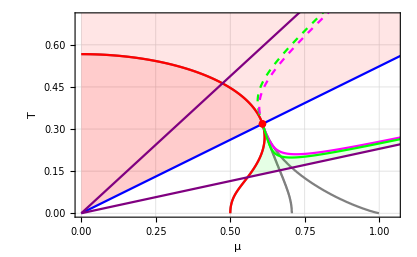

```mathematica
GN2`GLPhaseDiagram=Show[{
largeNnumRefPlot,
ParametricPlot[With[{T=GN2`TC(1-GN2`TCκ z^2)},{z T,T}],{z,0,200},PlotStyle->{Dashed,Dotted}],
Graphics[{Green,Opacity[0.1],Polygon[GN2`GLspinodalRegion]}],
Graphics[{Red,Opacity[0.1],Polygon[GN2`GLrestoredStableRegion]}],
Graphics[{Red,Opacity[0.2],Polygon[GN2`GLrestoredUnstableRegion]}],
ListLinePlot[{GN2`GLα20leftSpinodal,GN2`GLα20secondOrderPB},PlotStyle->{{Red},{Red}}],
Plot[1/Actor`DLi2`roots[[1]]T,{T,0,2},PlotStyle->{Blue}],
Plot[1/# T,{T,0,2},PlotStyle->{Purple}]&/@Actor`DLi4`roots,
ListLinePlot[GN2`GLrightSpinodal,PlotStyle->{Magenta}],
ListLinePlot[GN2`GLfirstOrderBP,PlotStyle->{Green}],
ListLinePlot[GN2`GLlines["α1stOPBα4"],PlotStyle->{{Green,Dashed}}],
ListLinePlot[GN2`GLlines["αrSLα4"],PlotStyle->{{Magenta,Dashed}}],
ListPlot[{{GN2`μCP,GN2`TCP}},PlotStyle->Red]
},PlotRange->{{0,1.05},{0,0.7}},PlotRangePadding->.01,Frame->True,GridLines->Automatic,FrameLabel->{"μ","T"}]
```

```mathematica
asoc=<|
"cp"->{GN2`μCP,GN2`TCP},
"ref"->1.*(largeNnumRef[#]&/@Keys[largeNnumRef][[6;;]]),
"2nd"->1.*GN2`GLα20secondOrderPBᵀ,
"lS"->1.*GN2`GLα20leftSpinodalᵀ,
"rS"->1.*GN2`GLrightSpinodalᵀ,
"1st"->1.*GN2`GLfirstOrderBPᵀ,
"a40"->({{0,0},{Actor`DLi2`roots[[1]]T,T}}/.T->2)ᵀ,
"a60"->({{0,0},{# T,T}}ᵀ&/@Actor`DLi4`roots/.T->2),
"testpts"->{{0,0.5169329586555488},{0,0.5669329586555488},{0,0.6169329586555489},{0.6039888921571371,0.25},{0.6139888921571371,0.25},{0.6217339277595166,0.25},{0.629478963361896,0.25},{0.632913785350291,0.25},{0.636348607338686,0.25},{0.646348607338686,0.25}}ᵀ
|>;
Export["../gn/figures/gn_gl_comp.json",asoc];
```

#### Landau theory of 2nd order PT

V_GL^2=β0+β2 Δ^2+β4 Δ^4;β4>0
β2>0: Δ=0: global minimum
β2<0: Δ=0: local maximum, Δ^2=-β2/(2 β4): global minium
β2=0_-: second order PT: global minium Δ^2=-β2/(2 β4) merges into local maximum at Δ=0, becoming the global minimum at and beyond β=0

https://en.wikipedia.org/wiki/Landau_theory
http://lampx.tugraz.at/~hadley/ss2/landau/second_order.php

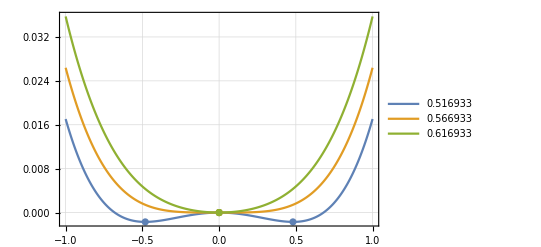

../gn/figures/gn_gl_2nd_U.json

```mathematica
testpts={0,GN2`TC+#}&/@{-0.05,0.,0.05};
potentials={#["U"],#["ΔrootsTable"],#["μ"],#["T"],#["αi"]}&/@(GL`potential`compute[#[[1]],#[[2]],GN2`α2nFunctions[[1;;3]]]&/@testpts);
ux=#[[1]][$x]-#[[1]][0]&/@%;
extrema=DeleteDuplicates[Flatten[#,1]]&/@(Map[p↦{{-p,#[[1]][p]-#[[1]][0]},{p,#[[1]][p]-#[[1]][0]}},#[[2]][[All,1]]]&/@%%);
data=Table[{$x,#},{$x,-1,1,5*10^-3}]&/@ux;
asoc=<|"extrema"->1*extrema,"muTi"->1*testpts,"data"->1*data|>;
Show[{ListLinePlot[data,PlotLegends->Placed[testpts[[All,2]],{Left,Top}]],ListPlot[extrema]},Frame->True,GridLines->Automatic]
Export["../gn/figures/gn_gl_2nd_U.json",asoc]
```

-(8 π^2 T^2 (-EulerGamma+Log[π]+Log[T]))/(7 Zeta[3])

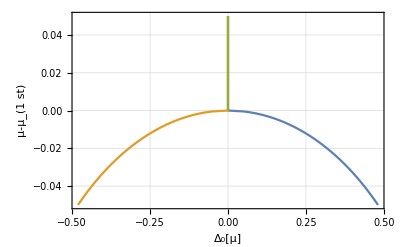

```mathematica
μ1st=testpts[[2,2]];
μL=testpts[[1,2]]-testpts[[2,2]];
μR=testpts[[3,2]]-testpts[[2,2]];
Δμ0=0;

xiR=Subdivide[μ1st+μL-Δμ0,μ1st+μR,200]~Join~{μ1st}//Sort//DeleteDuplicates;
Δ1=-α2/(2 α4)/.{α2->GN2`α2,α4->GN2`α4}/.μ->0//FunctionExpand
datR=Transpose[({{Re@√%,#-μ1st},{-Re@√%,#-μ1st}}/.{T->#,μ->0})&/@xiR];
xiR=Map[x↦If[x<μ1st+μL,0,If[x>μ1st+μR,-1,Floor[99*(x-μ1st-μL)/(μR-μL)]]],xiR];


xiL=Subdivide[μ1st,μ1st+μR+Δμ0,200]~Join~{μ1st}//Sort//DeleteDuplicates;
datL=Transpose[({{0,#-μ1st}}/.{T->#,μ->0})&/@xiL];
xiL=Map[x↦If[x<μ1st+μL,0,If[x>μ1st+μR,-1,Floor[99*(x-μ1st-μL)/(μR-μL)]]],xiL];

datR~Join~datL//ListLinePlot[#,PlotRange->Full,Frame->True,GridLines->Automatic,FrameLabel->{"Δ_0[μ]","μ-μ_(1  st)"}]&
<|"xiR"->xiR,"datR"->1.*datR,"xiL"->xiL,"datL"->1.*datL|>;
Export["../gn/figures/gn_gl_2nd_Umin.json",%];
```

```mathematica
(*Subscript[Δ, 0][T]=±√(-(Subscript[β, 2][T])/(2 Subscript[β, 4][T])),T<Subscript[T, C]*)
```

Re[PolyGamma[n_,x_]]:>1/2 (PolyGamma[n,x]+PolyGamma[n,ComplexExpand[Conjugate[x]]])

```mathematica
α0+α2 Δ^2+α4 Δ^4/.{α0->GN2`α0,α2->GN2`α2,α4->GN2`α4}//FunctionExpand;
f={%/.Δ->√(-(8 π^2 T^2 (-EulerGamma+Log[π]+Log[T]))/(7 Zeta[3])),%/.Δ->0}//Simplify;
f=%/.Actor`RePolyGammaToPolyGammaSum;
n=- D[f/.Actor`RePolyGammaToPolyGammaSum,μ]/.μ->0//Simplify;
χ= -D[f,μ,μ]/.μ->0;
```

```mathematica
α0+α2 Δ^2+α4 Δ^4/.{α0->GN2`α0,α2->GN2`α2,α4->GN2`α4}//FunctionExpand;
f={%/.Δ->√(-(8 π^2 T^2 (-EulerGamma+Log[π]+Log[T]))/(7 Zeta[3])),%/.Δ->0}/.μ->0//Simplify;
s=- D[%,T]//Simplify;
cv=T D[%,T];
```

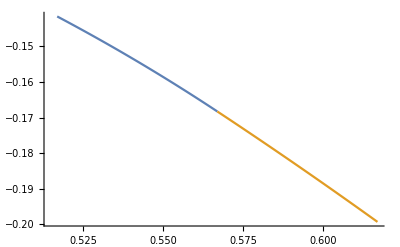
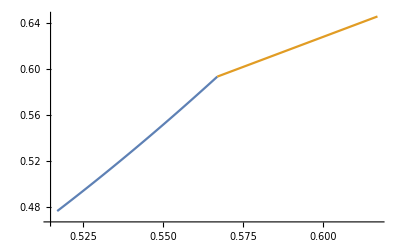
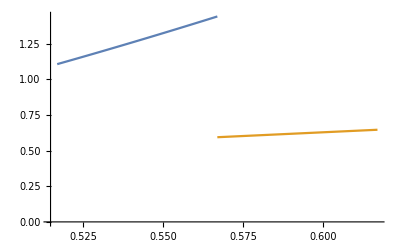
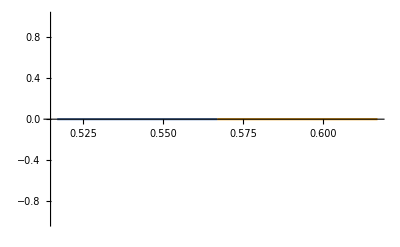
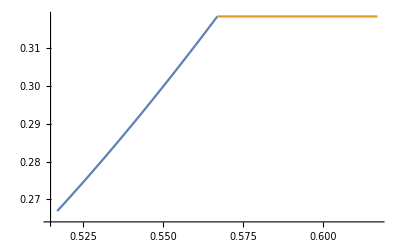

```mathematica
datLthermo=Table[{T,1.*f[[1]],1.*s[[1]],1.*cv[[1]],1.*n[[1]],1.*χ[[1]]}/.T->GN2`TC+0.05*t,{t,-1,0,1/100}];
datRthermo=Table[{T,1.*f[[2]],1.*s[[2]],1.*cv[[2]],1.*n[[2]],1.*χ[[2]]}/.T->GN2`TC+0.05*t,{t,0,1,1/100}];
Export["../gn/figures/gn_gl_2nd_datthermo.json",<|"datLthermo"->datLthermoᵀ,"datRthermo"->datRthermoᵀ|>];
ListLinePlot[{datLthermo[[All,{1,1+#}]],datRthermo[[All,{1,1+#}]]}]&/@{1,2,3,4,5}
```

```mathematica
GN2`TC//N
```

0.566933

#### Landau theory of 1st order PT

V_GL^3[Δ^2]=β0+β2 Δ^2+β4 Δ^4+β6 Δ^6;β6>0
β2<0: Δ=0 local Maximum, global minimum at Δ^2=-β4/(3 β6)+(√(β4^2-3 β2 β6))/(3 β6) which aproaches Δ=0 for β2→0_- again second order PT for  β2→0_- independent of β_4 in this case
β2>0,β4^2-3 β2 β6<0: local Minimum at Δ=0, restored phase
β2>0,β4<0,β4^2-3 β2 β6>0: local Minima at Δ=0, Δ^2=-β4/(3 β6)+(√(β4^2-3 β2 β6))/(3 β6), local maximum at Δ^2=-β4/(3 β6)-(√(β4^2-3 β2 β6))/(3 β6): Spinodal region
	β2→0_+: local maximum at Δ^2=-β4/(3 β6)-(√(β4^2-3 β2 β6))/(3 β6) vanishes into Δ=0, Δ=0 changes from a local minimum so a local maximum, left spinodal line (GL==physical)
	β4^2-3 β2 β6→0_+: local maximum at Δ^2=-β4/(3 β6)-(√(β4^2-3 β2 β6))/(3 β6)  approaches local minimum at Δ^2=-β4/(3 β6)+(√(β4^2-3 β2 β6))/(3 β6) which becomes a maximum, right spinodal line  (GL)
	β4→0_-: aproaching CP: all extrema merge into Δ=0
β2>0,β4<0,β4^2-3 β2 β6>0: V_GL^3[0]==V_GL^3[-β4/(3 β6)+(√(β4^2-3 β2 β6))/(3 β6)]⇒ β6 β2-β4^2/4==0, first order phase transition (GL)

https://en.wikipedia.org/wiki/Landau_theory
http://lampx.tugraz.at/~hadley/ss2/landau/first_order.php

{0.61398889215713711978,0.25}

{0.62947896336189602881,0.25}

{0.63634860733868600689,0.25}

0.62947896336189602881

-0.015490071204758909

0.0068696439767899781

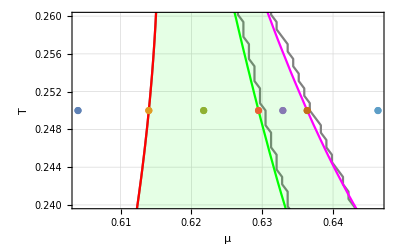

```mathematica
Ttest=0.25`32;
Δμ0=0.01;
{α0,α2,α4,α6}=#[μ,Ttest]&/@GN2`α2nFunctions;
pLS={μ,Ttest}/.FindRoot[0==α2,{μ,0.5`32},PrecisionGoal->16,AccuracyGoal->16,WorkingPrecision->20,MaxIterations->1000]
p1st={μ,Ttest}/.FindRoot[0==α2 α6-α4^2/4/.T->Ttest,{μ,0.5`32},PrecisionGoal->16,AccuracyGoal->16,WorkingPrecision->20,MaxIterations->1000]
pRS={μ,Ttest}/.FindRoot[0==α4^2-3α2 α6/.T->Ttest,{μ,0.5`32},PrecisionGoal->16,AccuracyGoal->16,WorkingPrecision->20,MaxIterations->1000]
testpts={pLS-{Δμ0,0},pLS,pLS+0.5(p1st-pLS),p1st,p1st+0.5*(pRS-p1st),pRS,pRS+{Δμ0,0}};

μ1st=(p1st)[[1]]
μL=(pLS-p1st)[[1]]
μR=(pRS-p1st)[[1]]

Show[{GN2`GLPhaseDiagram,ListPlot[{#}&/@testpts]},PlotRange->{{μ1st+μL-Δμ0,μ1st+μR+Δμ0},{Ttest-0.01,Ttest+0.01}}]
ClearAll[α0,α2,α4,α6]
```

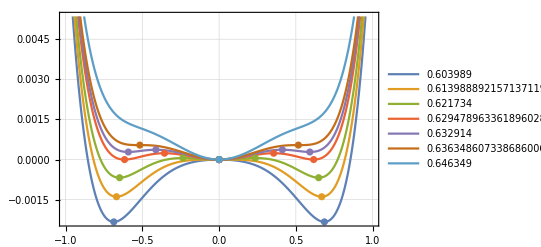

../gn/figures/gn_gl_1st_U.json

```mathematica
potentials={#["U"],#["ΔrootsTable"],#["μ"],#["T"],#["αi"]}&/@(GL`potential`compute[#[[1]],#[[2]],GN2`α2nFunctions[[1;;4]]]&/@testpts);
ux=#[[1]][$x]-#[[1]][0]&/@%;
extrema=DeleteDuplicates[Flatten[#,1]]&/@(Map[p↦{{-p,#[[1]][p]-#[[1]][0]},{p,#[[1]][p]-#[[1]][0]}},#[[2]][[All,1]]]&/@%%);
data=Table[{$x,#},{$x,-1,1,5*10^-3}]&/@ux;
asoc=<|"extrema"->1*extrema,"muTi"->1*testpts,"data"->1*data|>;
Show[{ListLinePlot[data,PlotLegends->Placed[testpts[[All,1]],{Left,Top}]],ListPlot[extrema]},Frame->True,GridLines->Automatic]
Export["../gn/figures/gn_gl_1st_U.json",asoc]
```

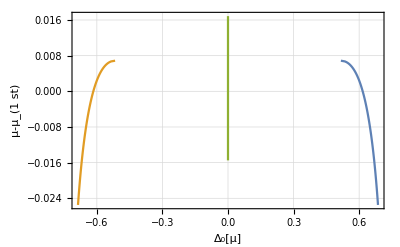

```mathematica
xiR=Subdivide[μ1st+μL-Δμ0,μ1st+μR,200]~Join~{μ1st}//Sort//DeleteDuplicates;
Δ1=-α4/(3 α6)+(√(α4^2-3 α2 α6))/(3 α6)/.{α2->GN2`α2,α4->GN2`α4,α6->GN2`α6};
datR=Transpose[({{Re@√%,#-μ1st},{-Re@√%,#-μ1st}}/.{T->Ttest,μ->#})&/@xiR];
xiR=Map[x↦If[x<μ1st+μL,0,If[x>μ1st+μR,-1,Floor[99*(x-μ1st-μL)/(μR-μL)]]],xiR];


xiL=Subdivide[μ1st+μL,μ1st+μR+Δμ0,200]~Join~{μ1st}//Sort//DeleteDuplicates;
datL=Transpose[({{0,#-μ1st}}/.{T->Ttest,μ->#})&/@xiL];
xiL=Map[x↦If[x<μ1st+μL,0,If[x>μ1st+μR,-1,Floor[99*(x-μ1st-μL)/(μR-μL)]]],xiL];

datR~Join~datL//ListLinePlot[#,PlotRange->Full,Frame->True,GridLines->Automatic,FrameLabel->{"Δ_0[μ]","μ-μ_(1  st)"}]&
<|"xiR"->xiR,"datR"->1.*datR,"xiL"->xiL,"datL"->1.*datL|>;
Export["../gn/figures/gn_gl_1st_Umin.json",%];
```

```mathematica
μ1st
```

0.62947896336189602881

```mathematica
μL-Δμ0
```

-0.0254901

```mathematica
f1list
f1listb
```

{{0.603989,-0.0931165},{0.613989,-0.0941136},{0.623989,-0.0951711}}

{{0.629479,-0.0957891}}

{0.62947896336189602881,0.6301659277595750266,0.6308528921572540244,0.6315398565549330222,0.63222682095261202,0.6329137853502910179,0.6336007497479700157,0.6342877141456490135,0.6349746785433280113,0.6356616429410070091,0.6363486073386860069}

```mathematica
GN2`α0+GN2`α2 Δ^2+GN2`α4 Δ^4+GN2`α6 Δ^6;
f={%/.Δ->√Δ1,%/.Δ->0}/.Actor`RePolyGammaIntRule[μ/T];
s=-D[f,T]/.T->Ttest;
cv=-T D[f,T,T]/.T->Ttest;
n=-D[f,μ]/.T->Ttest;
χq=-D[f,μ,μ]/.T->Ttest;
f=f/.T->Ttest;
```

```mathematica
thermo=Transpose[{#[[1]],#[[2]]}&/@{f,s,cv,n,χq}];
```

```mathematica
f1list=Transpose@Table[Flatten@{1.*μ,1.*thermo[[1]]},{μ,Subdivide[μ1st+μL-Δμ0,μ1st,100]}];
f1listb=Transpose@Table[Flatten@{1.*μ,1.*thermo[[1]]},{μ,Subdivide[μ1st,μR+μ1st,100]}];

f[[2]]/.T->Ttest;
f2list=Transpose@Table[Flatten@{1.*μ,1.*thermo[[2]]},{μ,Subdivide[μ1st,μ1st+μR+Δμ0,100]}];
f2listb=Transpose@Table[Flatten@{1.*μ,1.*thermo[[2]]},{μ,Subdivide[μ1st+μL,μ1st,100]}];
```

```mathematica
dat={f1list,f1listb,f2list,f2listb};
Export["../gn/figures/gn_gl_1st_datthermo.json",<|"dat"->%,"mu0"->μ1st+μL-Δμ0,"mu1"->μ1st+μR+Δμ0,"mu1st"->μ1st|>];
```

```mathematica
Ttest(f2list[[3,1]]-f1list[[3,-1]])//ScientificForm
```

7.22057×10^-3

#### n-T phase diagram

```mathematica
GN2`α0+GN2`α2 Δ^2+GN2`α4 Δ^4+GN2`α6 Δ^6//HornerForm[#,Δ]&;
f={%/.Δ->√Δ1,%/.Δ->0}/.Actor`RePolyGammaIntRule[μ/T];
test=Join[{T},-D[%,μ]];
nt2nd=Map[{test[[-1]],test[[1]]}/.{μ->#[[1]],T->#[[2]]}&,GN2`GLα20secondOrderPB];
```

```mathematica
nt1sta={Last[nt2nd]}~Join~Map[{test[[2]],test[[1]]}/.{μ->#[[1]],T->#[[2]]}&,GN2`GLfirstOrderBP[[2;;150]]];
```

```mathematica
nt1stb={Last[nt2nd]}~Join~Map[{test[[3]],test[[1]]}/.{μ->#[[1]],T->#[[2]]}&,GN2`GLfirstOrderBP[[2;;300]]];
```

```mathematica
<|"dat"->{1.*nt2ndᵀ,1.*Re[nt1sta]ᵀ,1.*nt1stbᵀ}|>;
Export["../gn/figures/gn_gl_ntPD.json",%]
```

../gn/figures/gn_gl_ntPT.json

## generalized GL analysis

GN2`gGLlines=GL`lines`compute[GN2`α2nFunctions,{{0.005,1},{0.005,1}},{4/3*5/36,4/3*3/8},{PerformanceGoal→"Quality",PlotPoints→40,MaxRecursion→4}];
SaveToCell[GN2`gGLlines,"GN2`gGLlines"]

```mathematica
GN2`gGLlines=;
```

```mathematica
Import["..\\gn\\anc\\largeN_pd_*.json"][[All,2]];
ref=Transpose["data"]/.#&/@%;
```

```mathematica
<|
"refHBPtoIP"->1.*ref[[1]]ᵀ,
"refIPtoSP"->1.*ref[[4]]ᵀ,
"refHBPtoSP"->1.*ref[[3]]ᵀ,
"refLP"->1.*{ref[[5]]}ᵀ,
"eta1"->1.*GN2`gGLlines["gGLη2HBPlines"][[1]]ᵀ,
"eta2"->1.*GN2`gGLlines["gGLη2SPlines"][[1]]ᵀ
|>;
Export["../gn/figures/ggl_pd.json",%]
```

../gn/figures/ggl_pd.json

```mathematica
4/3*5/36
4/3*3/8
```

5/27

1/2

```mathematica
5/27//N
```

0.185185